# IIR Filter design

A popular method of creating digital filters is to transform analog prototypes to their digital equivalents using the bilinear transformation. The result is an infinite impulse response (IIR) filter, represented as a Trasfer Function Model (which is a discrete–time approximation of an analog filter)

## Analog Filters

### Butterworth

Two parameters:

cutoff frequency

filter order (sharpness of the transition)

Frequency response is monotonic,

```mathematica
ButterworthFilterModel[4]
tf=ToDiscreteTimeModel[ButterworthFilterModel[4],1,z]
poles=TransferFunctionPoles[tf]
```

```mathematica
1./(((0.3826834323650898-0.9238795325112867 ⅈ)+s) ((0.3826834323650898+0.9238795325112867 ⅈ)+s) ((0.9238795325112867-0.3826834323650898 ⅈ)+s) ((0.9238795325112867+0.3826834323650898 ⅈ)+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s111.0.38268343236508981FalseFalseFalseAutomaticNoneAutomatic
```

```mathematica
(1. (1.+z)^4)/((4.525594951964848+2.220446049250313*^-16 ⅈ)-(28.642488842966955-8.881784197001252*^-16 ⅈ) z+(74.68629150101523-1.7763568394002505*^-15 ⅈ) z^2-91.35751115703303 z^3+(56.78811354701991-2.8843107672476197*^-16 ⅈ) z^4)1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z111.4.5255949519648481FalseFalseFalseAutomaticNoneAutomatic
```

{{{0.345005+0.176037 ⅈ,0.345005-0.176037 ⅈ,0.459366-0.565866 ⅈ,0.459366+0.565866 ⅈ}}}

```mathematica
1./(((0.3826834323650898-0.9238795325112867 ⅈ)+s) ((0.3826834323650898+0.9238795325112867 ⅈ)+s) ((0.9238795325112867-0.3826834323650898 ⅈ)+s) ((0.9238795325112867+0.3826834323650898 ⅈ)+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s111.0.38268343236508981FalseFalseFalseAutomaticNoneAutomatic
```

{{{-0.92388-0.382683 ⅈ,-0.92388+0.382683 ⅈ,-0.382683-0.92388 ⅈ,-0.382683+0.92388 ⅈ}}}

```mathematica
1./(((0.5-0.8660254037844386 ⅈ)+s) ((0.5+0.8660254037844386 ⅈ)+s) (1.+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s111.0.51FalseFalseFalseAutomaticNoneAutomatic
```

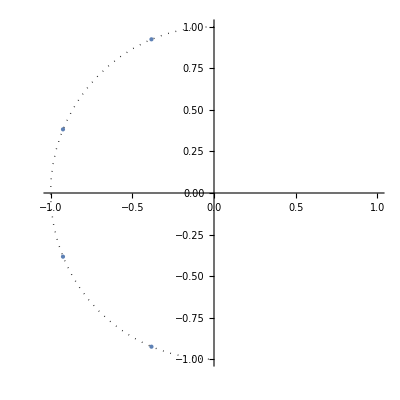

```mathematica
ListPlot[{Re[#],Im[#]}&/@poles[[1,1]],PlotRange->{{-1,1},{-1,1}},PlotStyle->PointSize[Large],Epilog->{Dotted,Circle[{0,0},1,{Pi/2,3Pi/2}]},AspectRatio->1,PlotRangePadding->0.1]
```

## Projektowanie filtrów cyfrowych Butterwortha i Czebyszewa

Układ analogowy jet stabilny, jeżeli bieguny jego transmitancji leżą w lewej półpłaszczyźnie płaszczyzny zespolonej

Układ dyskretny jest stabilny, jeżeli bieguny jego transmitancji leżą wewnątrz okręgu jednostkowego na płaszczyźnie zespolonej.

Dla układu analogowego osią częstotliwości jest oś urojona s=jω.
Dla układu dyskretnego częstotliwość zmiania się po okręgu jednostkowym z=e^jΩ.

W przypadku biegunów na osi (dla analogowych) lub na okręgu (dla dyskretnych) stabilność jest warunkowa, a układ odpowiada oscylacją.

Częstotliwość końca pasma przepustowego (f_P) w dB

Największe dopuszczalne tłumienie w paśmie przepustowym (A_p) dla filtru Czebyszewa ten parametr określa jednocześnie dopuszczalne zafalowanie charakterystyki amplitudowej w paśmie przepustowym (w kHz)

Częstotliwość początku pasma zaporowego (f_S) w dB

Wymagane minimalne tłumienie w paśmie zaporowym (A_s) (w kHz)

```mathematica
Ap=0.5; 
fp=3;
Ar=20;
fr=7;
```

### Obliczenie rzędu filtru

#### Współczynnik selektywności k

k=f_P/f_R

```mathematica
k[fp_,fr_]:=fp/fr;
```

#### Współczynnik dyskryminacji d

d=√((10^(0.1 A_P)-1)/(10^(0.1 A_R)-1))

```mathematica
d[Ap_,Ar_]:=√((10^(0.1 Ap)-1)/(10^(0.1 Ar)-1));
```

Rząd filtru Butterwortha oblicza się ze współczynników k i d

n=(|log d|)/(|log k|)

```mathematica
nbutt[d_,k_]:=Abs[Log[d]]/Abs[Log[k]];
```

```mathematica
nb=nbutt[d[Ap,Ar],k[fp,fr]]
```

3.95298

Rząd filtru Czebyszewa określa się z podobnego wzoru:

n=(arc cosh(1/d))/(arc cosh(1/k))

```mathematica
nczeb[d_,k_]:=ArcCos[1/d]/ArcCos[1/k];
```

```mathematica
nc=nczeb[d[Ap,Ar],k[fp,fr]]
```

2.71107+0. ⅈ

Rząd filtru nie może być ułamkowy, więc zaokrąglamy w górę.

```mathematica
nb=Ceiling[nb]
nc=Ceiling[nc]
```

4

3

Rząd filtr Czebyszewa będzie zawsze mniejszy lub równy rzędowi filtru Butterwortha

### Częstotliwość graniczna

W dolnoprzepustowym filtrze Czebyszewa jest to częstotliwość, dla której tłumienie filtru nie przekracza założonych zafalowań charakterystyki. A więc poprostu f_p

f_g=f_p

```mathematica
fgc=fp;
```

Dla filtru Butterwortha, częstotliwość graniczna to taka dla której następuje spadek wzmocnienia o 3 dB względem sygnału stałego (o częstotliowści 0). Jest ona większa od f_p jeżeli A_p jest mniejsze niż 3 dB. Można ją określić ze wzoru

f_g=f_p/((10^(0.1 A_p)-1)^(1/(2n)))

```mathematica
fg[fp_,Ap_,n_]:=fp/(10^(0.1 Ap)-1)^(1/(2n));
```

```mathematica
fgb=fg[fp,Ap,4]
```

3.90228

### Filtr prototypowy

Filtr prototypowy ≡ filtr anaologowy którego częstotliwość graniczna wynosi 1 Hz.

#### Butterworth

Kradraw charakterystyki amplitudowej definiuje się następująco

(|H(jω)|)^2=1/(1+(jω/j ω_(3 dB))^(2N))

|H(jω)|=√(1/(1+(jω/j ω_(3 dB))^(2N)))

gdzie ω_(3 dB) jest pulsacją, dla której charakterystyka amplitudowa opada do poziomu 1/(√2) (3 dB w skali decybelowej 20 log_10(1/√2)=-3dB. Rozważając zera mianownika:

1+(s/j ω_(3dB))^(2N)=0

Otrzymujemy bieguny transmitancji filtra Butterwortha:

```mathematica
sol=Solve[1+(s/(ⅈ ω))^(2NN)==0&&NN>0,s,Complexes]
```

{{s→ConditionalExpression[ⅈ ⅇ^((ⅈ (π+2 π C[1]))/(2 NN)) ω,(C[1]∈Integers&&-1+2 NN-2 C[1]≥0&&C[1]≥0)||(C[1]∈Integers&&C[1]≤-1&&1+2 NN+2 C[1]>0)]}}

```mathematica
sol[[1,1,2,1]]
```

ⅈ ⅇ^((ⅈ (π+2 π C[1]))/(2 NN)) ω

ω_(3dB)ⅇ^(j (π/(2N))(2k+N-1))

Do filtru wybieramy tylko te znajdujące się w lewej półpłaszczyźnie

```mathematica
roots[k_,N_]:=Exp[ⅈ(π/(2N))(2k+N-1)];
NN=2;
rootsbutt=N@Table[roots[i,NN],{i,0,NN}];
selrootbutt=s-Select[rootsbutt,Re[#]<=0&];
1/Times[selrootbutt/.{List->Sequence}]
```

1/(((0.707107-0.707107 ⅈ)+s) ((0.707107+0.707107 ⅈ)+s))

Z równania (Section.EquationNumbered) otrzymujemy:

20 log_10(1/√(1+(ω_p/ω_(3dB))^(2N)))=-A_p

20 log_10(1/√(1+(ω_s/ω_(3dB))^(2N)))=-A_s

Skąd rząd filtru:

N=1/2 log_10((10^(A_p/10)-1)/(10^(A_s/10)-1))/log_10(ω_p/ω_s)

ω_(3dB)=ω_pass/((10^(A_p/10)-1)^(1/(2N)))

### Składanie w całość dla Butterworth

```mathematica
Ap=0.5; 
fp=3;
As=20;
fs=7;
```

```mathematica
NButterworth[Ap_,As_,fp_,fs_]:=Ceiling[1/2 Log10[(10^(Ap/10)-1)/(10^(As/10)-1)]/Log10[fp/fs]];
```

```mathematica
f3dB[fp_,Ap_,NN_]:=fp/((10^(Ap/10)-1)^(1/(2NN)));(**pulsacja**)
```

```mathematica
NN=NButterworth[Ap,As,fp,fs]
f3dB[fp,Ap,NN]
```

4

3.90228

```mathematica
roots[k_,N_]:=f3dB[fp,Ap,NN]Exp[ⅈ(π/(2N))(2k+N-1)];
rootsbutt=N@Table[roots[i,NN],{i,0,NN}];
selrootbutt=s-Select[rootsbutt,Re[#]<=0&];
ButterworthFilter[ω_]:=f3dB[fp,Ap,NN]^NN/Times[selrootbutt/.{List->Sequence}]/.{s->ⅈω}
```

231.885/(((1.49334-3.60523 ⅈ)+ⅈ ω) ((1.49334+3.60523 ⅈ)+ⅈ ω) ((3.60523-1.49334 ⅈ)+ⅈ ω) ((3.60523+1.49334 ⅈ)+ⅈ ω))

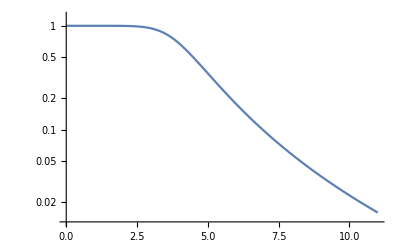

```mathematica
ButterworthFilter[ω]
LogPlot[Abs[ButterworthFilter[ω]],{ω,0,11},PlotRange->Full]
```

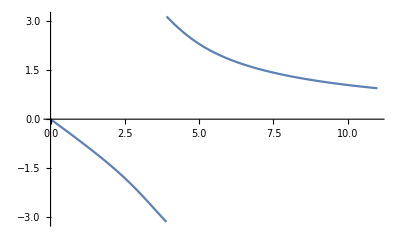

```mathematica
Plot[Arg[ButterworthFilter[ω]],{ω,0,11},PlotRange->Full]
```

### Dla Czebyszewa

(|H(jω)|)^2=1/(1+ϵ^2 V_N^2(ⅈω/ⅈ ω_(3dB)))

Gdzie

V_N(x)=Piecewise[{{cos(N arccos(x)), |x|≤1}, {cosh(Narccosh(x)), |x|>1}}]

Jest to filtr I typu. Charakterystyka jest równomiernie falista w paśmie przepustowym.
Amplituda zafalowania jest regulowana parametrem ϵ. 
W paśmie zaporowym charakterystyka opada monotonicznie

Dla filtru typu II jest odwrotnie. Charakterystyka jest płaska w paśmie przepustowym i równomiernie falista w paśmie zaporowym. 
Parametr ϵ reguluje amplitudę zafalowania charakterystyki amplitudowej w paśmie zaporowym.

(|H(jω)|)^2=1/(1+1/(ϵ^2 V_N^2(ⅈω_(3dB)/ⅈω)))

### Filtr eliptyczny

Do aproksymacji idealnej, prostokątnej charakterystyki częstotliwościowej w przypadku filtra eliptycznego stosuje się eliptyczną funkcję Jacobiego. 
Charakterystyka amplitudowa filtra eliptycznego jest równomiernie falista w paśmie przepustowym i zaporowym. Filtr eliptyczny opisują 4 parametry: N – rząd filtra, ω - krawędź pasma przepustowego, A_p oraz A_s.

### Transformacja częstotliwości

Low pass | s'=s/ω_0
High pass | s'=ω_0/s
Band pass | s'=ω_0/Δω((s/ω_0)^2+1)/(s/ω_0)
Band stop | s'=Δω/ω_0(s/ω_0)/((s/ω_0)^2+1)

where Δω=ω_2-ω_1 and ω_0=√(ω_1 ω_2)

### Transformacja biliniowa

s=2/Δt((1-z^-1)/(1+z^-1))

```mathematica
z/.Solve[s==2/Δt((1-z^-1)/(1+z^-1)),z][[1]]
```

(-2-s Δt)/(-2+s Δt)

ω=2/Δt tg(Ω/2)

Ω=arc tg(ω Δt/2)

## Projekt filtru dolnoprzepustowego

częstotliwość próbkowania f_pr=100Hz
krawędź pasma przepustowego f_1=20Hz
krawędź pasma zaporowego f_2=25Hz
nieliniowość charakterystyki w paśmie przepustowym r_p=3 dB
nieliniowość charakterystyki w paśmie zaporowym r_s=30dB

Przeliczenie częstotliwości filtra cyfrowego f_1 i f_2 na pulsację Ω w radianach:

Ω_1=2π f_1/f_pr=2π 20/100=1.2566 rad

Ω_2=2π f_2/f_pr=2π 25/100=1.5708 rad

```mathematica
A1=3;
f1=20;
A2=30;
f2=25;
fp=100;
```

```mathematica
Ω1=N@2π f1/fp
Ω2=N@2π f2/fp
```

1.25664

1.5708

### Krawędź pasma filtru analogowego

ω_1=2/(2Δt)tan(Ω_1/2)=2/(1/100)tan(1.2566/2)=145.3085 rad/s

ω_2=200 rad/s

```mathematica
ω1=2/(1/fp)Tan[Ω1/2]
ω2=2/(1/fp)Tan[Ω2/2]
fa1=1/(2π)ω1;
fa2=1/(2π)ω2;
```

145.309

200.

### Określenie parametrów filtru analogowego na podstawie podanych wymagań

```mathematica
NButterworth[Ap_,As_,fp_,fs_]:=Ceiling[1/2 Log10[(10^(Ap/10)-1)/(10^(As/10)-1)]/Log10[fp/fs]];
```

```mathematica
f3dB[fp_,Ap_,NN_]:=fp/((10^(Ap/10)-1)^(1/(2NN)));(**pulsacja**)
```

```mathematica
NN=NButterworth[A1,A2,fa1,fa2]
N@f3dB[ω1,A1,NN]
```

11

145.34

```mathematica
roots[k_,N_]:=f3dB[ω1,A1,NN]Exp[ⅈ(π/(2N))(2k+N-1)];
rootsbutt=N@Table[roots[i,NN],{i,0,NN}];
selrootbutt=s-Select[rootsbutt,Re[#]<=0&];
ButterworthFilter[ω_]:=f3dB[ω1,A1,NN]^NN/Times[selrootbutt/.{List->Sequence}]
```

### Filtr analogowy

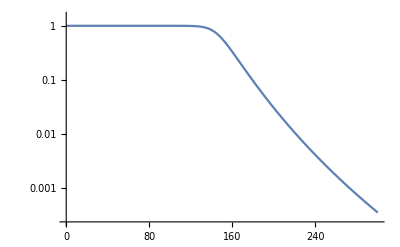

```mathematica
LogPlot[{Abs[ButterworthFilter[s]/.{s->ⅈ ω}]},{ω,0,300},PlotRange->Full]
```

### Przejście na filtr cyfrowy (w dziedzienie pulsacji/częstości)

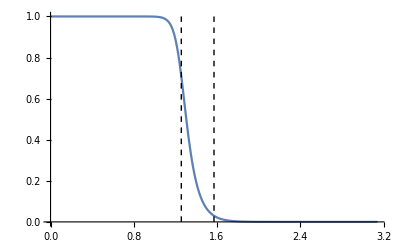

```mathematica
Plot[Abs[ButterworthFilter[s]/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}],{Ω,0,π},PlotRange->Full,Epilog->{Dashing[0.01],Line[{{Ω1,0},{Ω1,1}}],Line[{{Ω2,0},{Ω2,1}}]}]
```

```mathematica
N@1/10^(3/10)
N@1/10^(30/10)
```

0.501187

0.001

```mathematica
UnitConvert[Quantity[1,"SpeedOfLight"]*Quantity[1,"PlanckConstant"]/Quantity[1,"PlanckLength"],"eV"]
```

7.671×10^28 eV

### Filtr cyfrowy w dziedzinie częstotliwości

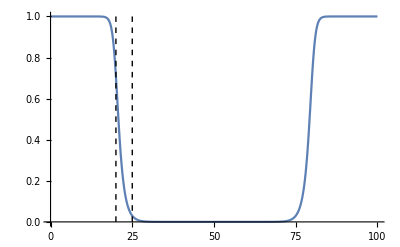

```mathematica
Plot[Abs[ButterworthFilter[s]/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}/.{Ω->f (2π)/fp}],{f,0,100},PlotRange->Full,Epilog->{Dashing[0.01],Line[{{f1,0},{f1,1}}],Line[{{f2,0},{f2,1}}]}]
```

## Reakcja filtru Butterworth na częstotliwości odcięcia

```mathematica
Manipulate[NButterworth[A1,A2,x,y],{x,0,100},{y,x,100},{A1,0,100,1},{A2,0,100,1}]
```

Obserwacja: im częstotliwości bliższe sobie, a za tem im bardziej stromy filtr tym wyższy rząd filtru Butterworth’a jest wymagany.

Oprócz tego dla:
(2.2,2.3)→N=78
(22.2,22.3)→N=769
(82.2, 82.3)→N=2843
a więc rząd filtru rośnie także z częstotliwością przy stałej różnicy f_2-f_1.

## Analiza filtrów Butterwortha w Mathematica

```mathematica
DiscretizeData[x_,bits_]:=Module[{max},max=Max[Abs[x]]; If[#>0,1,-1]Round[(Abs[#]/max)(Power[2,bits-1]-1)] max/(Power[2,bits-1]-1) &/@x];
```

```mathematica
num=Numerator@ButterworthFilter[s];
```

```mathematica
Denominator@ButterworthFilter[s]
```

((20.684-143.861 ⅈ)+s) ((20.684+143.861 ⅈ)+s) ((60.3764-132.206 ⅈ)+s) ((60.3764+132.206 ⅈ)+s) ((95.1774-109.841 ⅈ)+s) ((95.1774+109.841 ⅈ)+s) ((122.268-78.5767 ⅈ)+s) ((122.268+78.5767 ⅈ)+s) ((139.453-40.947 ⅈ)+s) ((139.453+40.947 ⅈ)+s) (145.34+s)

```mathematica
reals=Re[#]&/@(s/.Solve[Denominator@ButterworthFilter[s]==0,s])
imags=Im[#]&/@(s/.Solve[Denominator@ButterworthFilter[s]==0,s])
```

{-145.34,-139.453,-139.453,-122.268,-122.268,-95.1774,-95.1774,-60.3764,-60.3764,-20.684,-20.684}

{0,-40.947,40.947,-78.5767,78.5767,-109.841,109.841,-132.206,132.206,-143.861,143.861}

```mathematica
coeffs=Join[reals,imags];
{realsD,imagsD}=Partition[DiscretizeData[coeffs,6],Length@coeffs/2]
```

{{-143.861,-139.22,-139.22,-120.657,-120.657,-97.4539,-97.4539,-60.3286,-60.3286,-18.5626,-18.5626},{0.,-41.766,41.766,-78.8913,78.8913,-111.376,111.376,-129.939,129.939,-143.861,143.861}}

```mathematica
denomD=s-(realsD+ⅈ imagsD)/.{List->Times}
```

((18.5626-143.861 ⅈ)+s) ((18.5626+143.861 ⅈ)+s) ((60.3286-129.939 ⅈ)+s) ((60.3286+129.939 ⅈ)+s) ((97.4539-111.376 ⅈ)+s) ((97.4539+111.376 ⅈ)+s) ((120.657-78.8913 ⅈ)+s) ((120.657+78.8913 ⅈ)+s) ((139.22-41.766 ⅈ)+s) ((139.22+41.766 ⅈ)+s) ((143.861+0. ⅈ)+s)

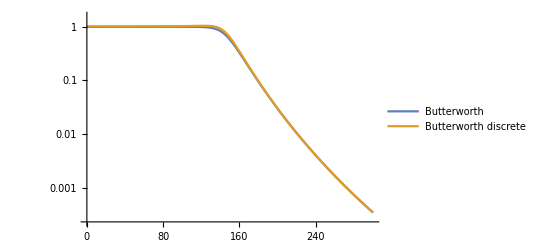

```mathematica
LogPlot[{Abs[ButterworthFilter[s]/.{s->ⅈ ω}],Abs[num/denomD/.{s->ⅈω}]},{ω,0,300},PlotRange->Full,PlotLegends->{"Butterworth","Butterworth discrete"}]
```

W dziedzinie pulsacji, łatwiej będzie obliczyć błąd

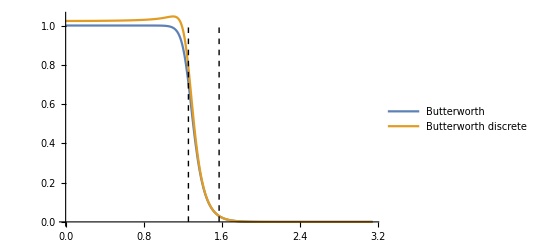

```mathematica
Plot[{Abs[ButterworthFilter[s]/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}],Abs[num/denomD/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}]},{Ω,0,π},PlotRange->Full,Epilog->{Dashing[0.01],Line[{{Ω1,0},{Ω1,1}}],Line[{{Ω2,0},{Ω2,1}}]},PlotLegends->{"Butterworth","Butterworth discrete"}]
```

```mathematica
CalcError[filtr_,filtrD_]:=Sqrt[NIntegrate[Abs[filtr-filtrD]^2,{Ω,0,π},AccuracyGoal->5,MaxRecursion->20]/NIntegrate[Abs[filtr]^2,{Ω,0,π},AccuracyGoal->5,MaxRecursion->20]]
```

```mathematica
CalcError[ButterworthFilter[s]/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ},num/denomD/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}]
```

0.0439729

Uzyskaliśmy w ten sposób średni błąd względny dla pewnego filtru Butterwortha, przy dyskretyzacji do 8-miu bitów.
Teraz uogólnimy tę procedurę i wykreślimy błąd w zależności od ilości bitów

### Błąd w zależności od ilości bitów

```mathematica
filtersD=Table[num/(MapThread[s-(#1+ⅈ #2)&,Partition[DiscretizeData[coeffs,i],Length@coeffs/2]]/.{List->Times}),{i,4,32,2}];
```

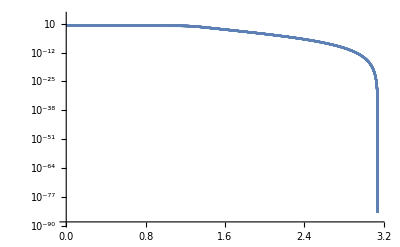

```mathematica
LogPlot[Abs[#/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}]&/@filtersD,{Ω,0,π},PlotRange->Full]
```

```mathematica
errors=CalcError[ButterworthFilter[s]/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ},#/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}]&/@filtersD
```

{0.0807374,0.0439729,0.00941541,0.0052734,0.000730413,0.000199079,0.0000632721,3.97357×10^-6,6.46014×10^-7,5.85675×10^-7,1.50606×10^-7,5.29091×10^-8,5.92378×10^-9,1.83285×10^-9,9.99849×10^-11}

```mathematica
bits=Range[4,32,2];
```

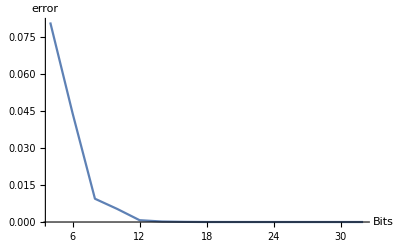

```mathematica
ListLinePlot[{bits,errors}ᵀ,PlotRange->Full,AxesLabel->{"Bits","error"}]
```

## Analiza względem wszystkich parametrów

Badanie rzędu filtru Butterwortha, Czebyszewa i Eliptycznego

```mathematica
q[k_]:=u+2 u^5+15 u^9+150 u^13/.{u->(1-(1-k^2)^(1/4))/(2(1+(1-k^2)^(1/4)))}
```

```mathematica
Manipulate[Plot3D[{1/2 Log10[(10^(A1/10)-1)/(10^(A2/10)-1)]/Log10[x],ArcCosh[1/(√((10^(A1/10)-1)/(10^(A2/10)-1)))]/ArcCosh[1/x],Log10[16(10^(A1/10)-1)/(10^(A2/10)-1)]/Log10[1/q[x]]},{x,0.000001,1},{A1,1,A2},AxesLabel->{"f_1/f_2","A1","N"},PlotLegends->{"Butterworth","Czebyszev","Eliptic"},ImageSize->Large,PlotRange->{{0,1},{1,A2},{0,15}}],{A2,2,100}]
```

```mathematica
DiscretizeList[x_,bits_]:=Module[{max},max=Max[Abs[x]]; If[#>=0,1,-1]Round[(Abs[#]/max)(Power[2,bits-1]-1)] max/(Power[2,bits-1]-1) &/@x];
DiscretizeComplexList[x_,bits_]:=Module[{reals,imags,coeffs,realsD,imagsD},
If[x=={},{},
reals=Re[#]&/@x;
imags=Im[#]&/@x;
coeffs=Join[reals,imags];
{realsD,imagsD}=Partition[DiscretizeList[coeffs,bits],Length@coeffs/2];
(realsD+ⅈ imagsD)]
];
CalcError[filtr_,filtrD_]:=Sqrt[NIntegrate[Abs[filtr-filtrD]^2,{Ω,0,π},AccuracyGoal->5,MaxRecursion->20]/NIntegrate[Abs[filtr]^2,{Ω,0,π},AccuracyGoal->5,MaxRecursion->20]];
```

```mathematica
DiscretizedModel[tf_,bits_]:=Module[{tfD,coeff,zeros,poles},
(*coeff=First@Flatten[Chop@Coefficient[Numerator[tf[s]],s,0]];*)
coeff=First[Flatten[Numerator[tf[s]]]];
coeff=If[Length[coeff]>0,coeff[[1]],coeff];
zeros=(s/.Solve[Numerator@(tf[s])==0,s])/.{s->{}};
poles=(s/.Solve[Denominator@(tf[s]/coeff)==0,s]);
coeff(s-DiscretizeComplexList[zeros,bits]/.{List->Times})/(s-DiscretizeComplexList[poles,bits]/.{List->Times})
];
```

### błędy

```mathematica
models=Table[ButterworthFilterModel[{"Lowpass",{1.k,1.},{1,i}},s],{k,0.1,0.9,0.1},{i,2,20,1}];
modelsD=Map[(DiscretizedModel[#,6])&,models,{2}];
errors=MapThread[First@Flatten@CalcError[#1[I Ω],#2/.{s->I Ω}]&,{models,modelsD},2];
ListPlot3D[errors,DataRange->{{2,20},{0.1,0.9}},AxesLabel->{"A2","k","Error"},ImageSize->Large]
```

-Graphics3D-

```mathematica
models=Table[Chebyshev1FilterModel[{"Lowpass",{1.k,1.},{1,i}},s],{k,0.1,0.9,0.01},{i,2,20,0.5}];
modelsD=Map[(DiscretizedModel[#,6])&,models,{2}];
errors=MapThread[First@Flatten@CalcError[#1[I Ω],#2/.{s->I Ω}]&,{models,modelsD},2];
ListPlot3D[errors,DataRange->{{2,20},{0.1,0.9}},AxesLabel->{"A2","k","Error"},ImageSize->Large]
```

-Graphics3D-

```mathematica
models=Table[EllipticFilterModel[{"Lowpass",{1.k,1.},{1,i}},s],{k,0.1,0.9,0.1},{i,2,20,0.5}];
modelsD=Map[(DiscretizedModel[#,6])&,models,{2}];
errors=MapThread[First@Flatten@CalcError[#1[I Ω],#2/.{s->I Ω}]&,{models,modelsD},2];
ListPlot3D[errors,DataRange->{{2,20},{0.1,0.9}},AxesLabel->{"A2","k","Error"},ImageSize->Large]
```

-Graphics3D-

## Zależność błędu od rzędu filtra

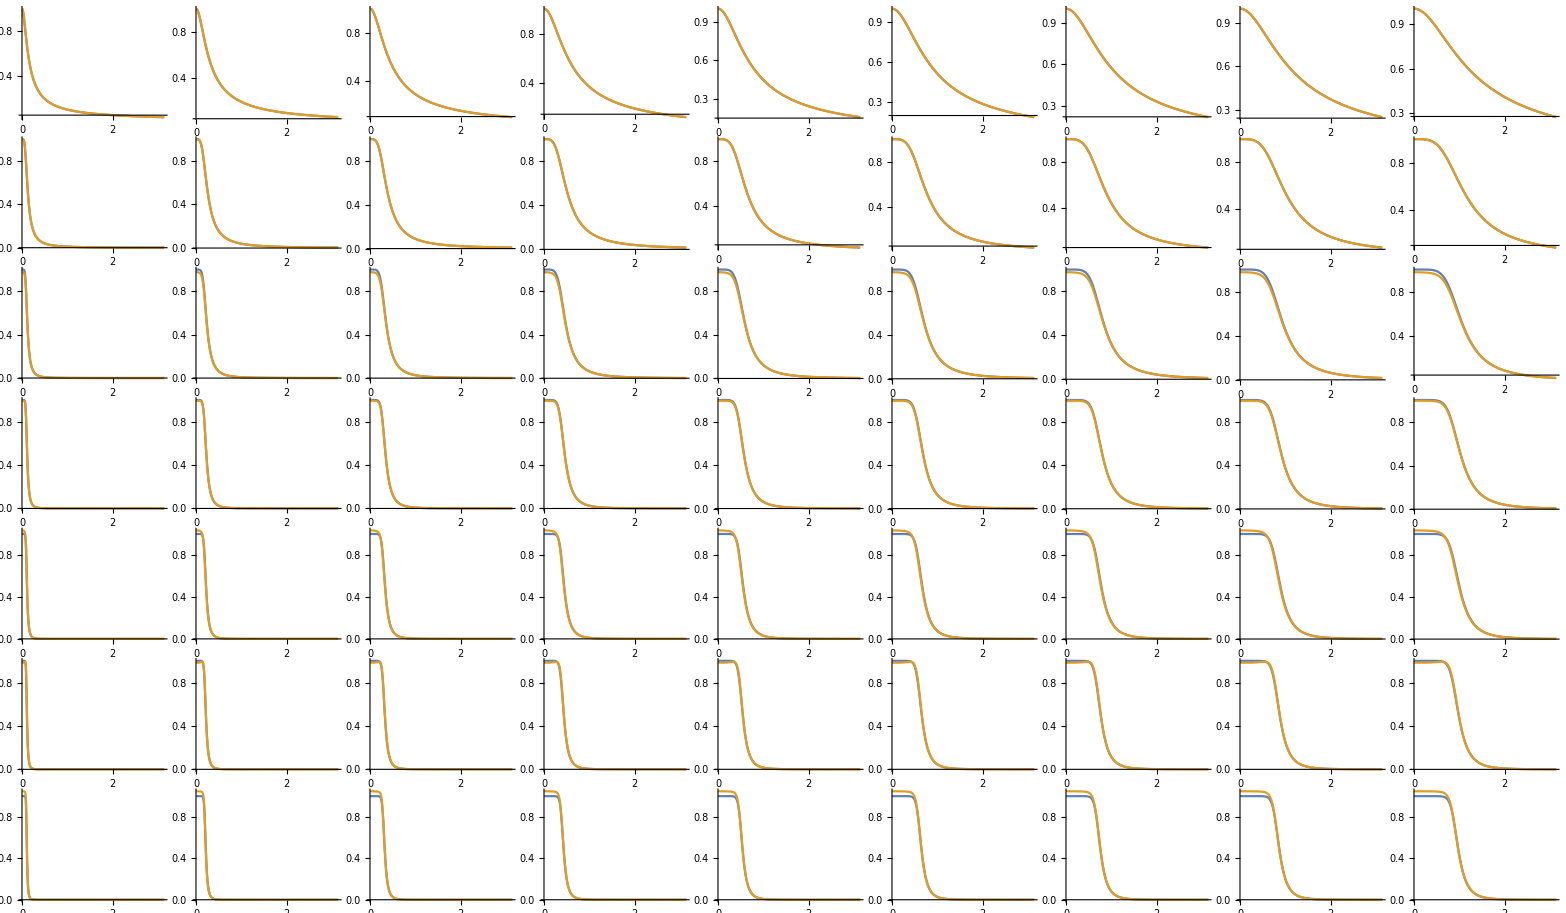

```mathematica
models=Table[ButterworthFilterModel[{"Lowpass" ,n,k},s],{n,1,7,1},{k,0.1,0.9,0.1}];
modelsD=Map[(DiscretizedModel[#,6])&,models,{2}];
errors0=MapThread[First@Flatten@CalcError[#1[I Ω],#2/.{s->I Ω}]&,{models,modelsD},2];
Grid@MapThread[Plot[{Abs[#1[I Ω]],Abs[#2]/.{s->I Ω}},{Ω,0,π},PlotRange->Full]&,{models,modelsD},2]
```

```mathematica
ListPlot3D[errors0,DataRange->{{0.1,0.9},{1,7}},AxesLabel->{"k","N","Error"},ImageSize->Large]
```

-Graphics3D-

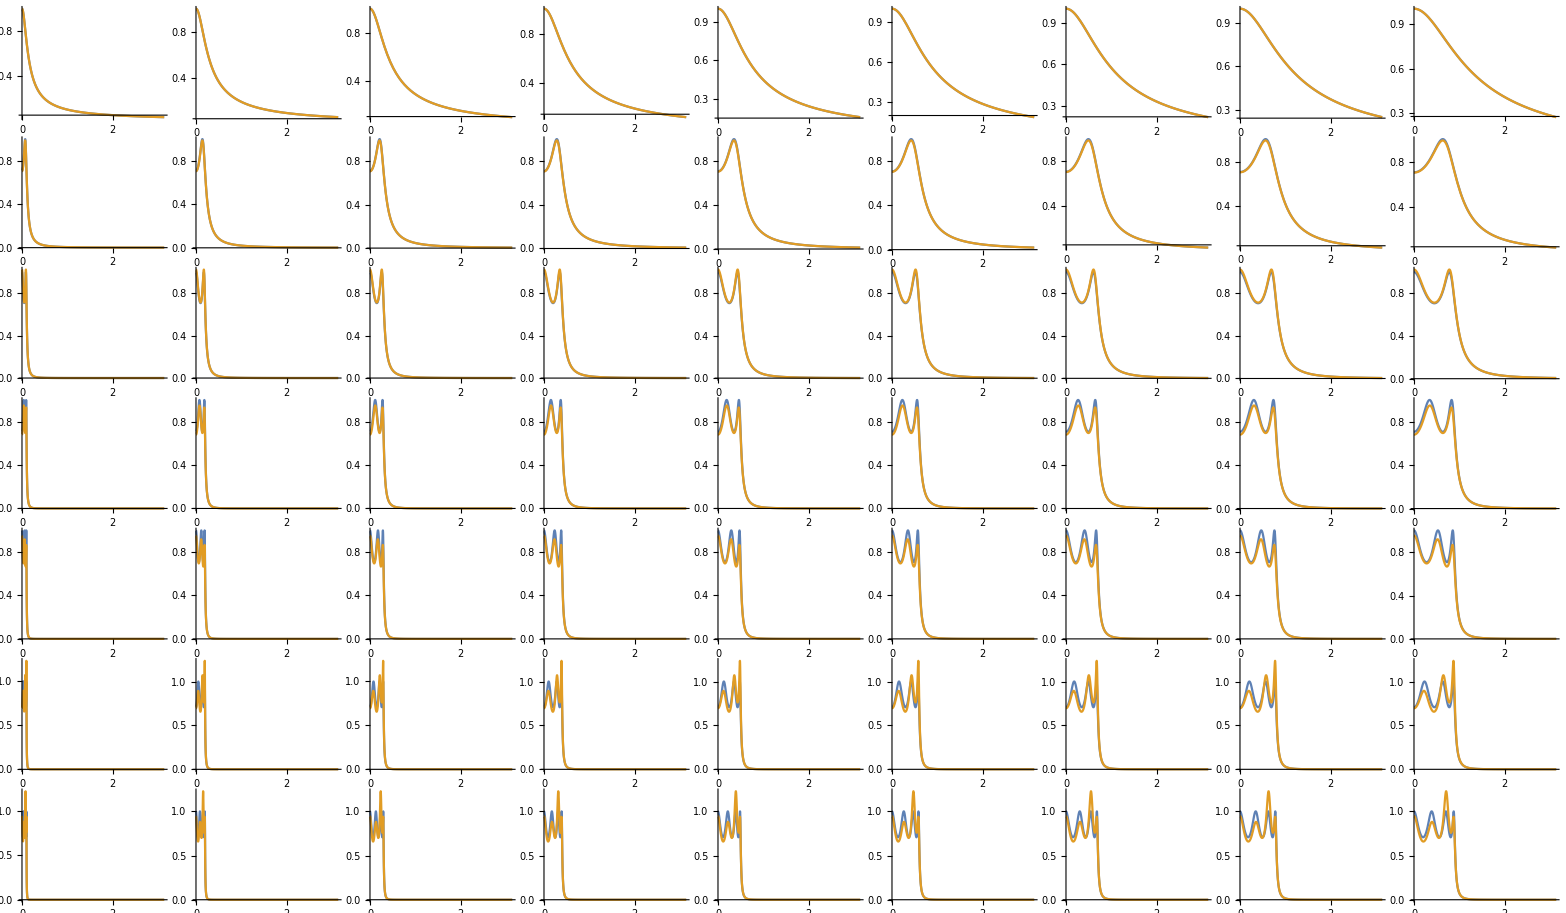

-Graphics3D-

```mathematica
models=Table[Chebyshev1FilterModel[{"Lowpass" ,n,k},s],{n,1,7,1},{k,0.1,0.9,0.1}];
modelsD=Map[(DiscretizedModel[#,6])&,models,{2}];
errors1=MapThread[First@Flatten@CalcError[#1[I Ω],#2/.{s->I Ω}]&,{models,modelsD},2];
Grid@MapThread[Plot[{Abs[#1[I Ω]],Abs[#2]/.{s->I Ω}},{Ω,0,π},PlotRange->Full]&,{models,modelsD},2]
ListPlot3D[errors1,DataRange->{{0.1,0.9},{1,7}},AxesLabel->{"k","N","Error"},ImageSize->Large]
```

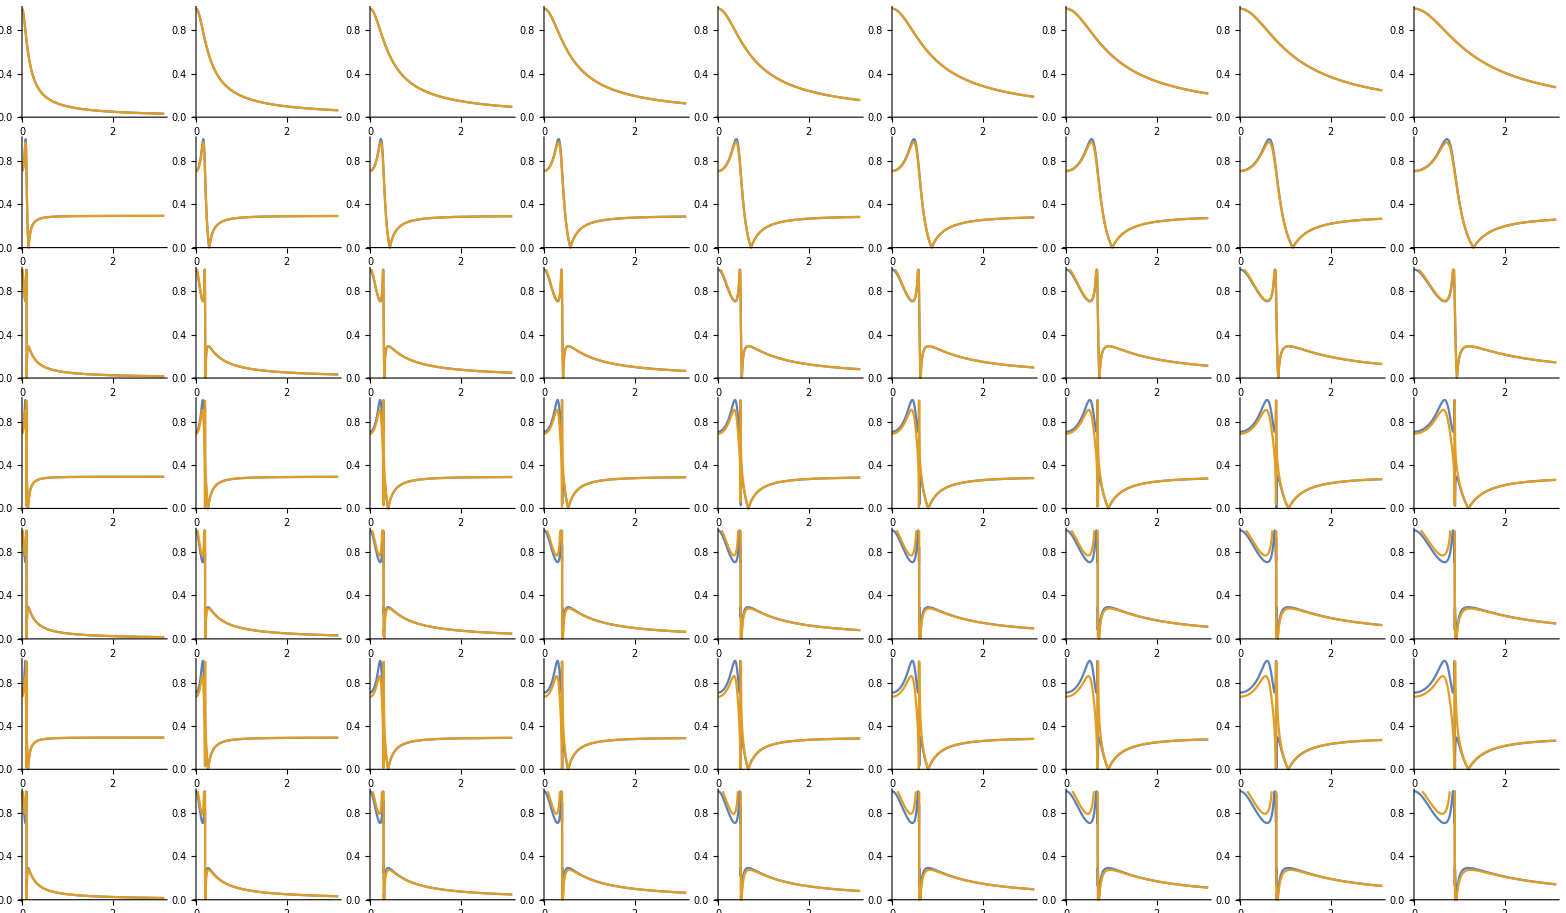

-Graphics3D-

```mathematica
models=Table[EllipticFilterModel[{n,k},s],{n,1,7,1},{k,0.1,0.9,0.1}];
modelsD=Map[(DiscretizedModel[#,6])&,models,{2}];
errors2=MapThread[First@Flatten@CalcError[#1[I Ω],#2/.{s->I Ω}]&,{models,modelsD},2];
Grid@MapThread[Plot[{Abs[#1[I Ω]],Abs[#2]/.{s->I Ω}},{Ω,0,π},PlotRange->{{0,π},{0,1}}]&,{models,modelsD},2]
ListPlot3D[errors2,DataRange->{{0.1,0.9},{1,7}},AxesLabel->{"k","N","Error"},ImageSize->Large]
```

```mathematica
ListPlot3D[errors2,DataRange->{{0.1,0.9},{1,7}},AxesLabel->{"k","N","Error"},ImageSize->Large,PlotRange->{{0.1,0.9},{1,7},{0,1}}]
```

-Graphics3D-

```mathematica
ListPlot3D[{errors0,errors1,errors2},DataRange->{{0.1,0.9},{1,7}},AxesLabel->{"k","N","Error"},ImageSize->Large,PlotLegends->{"Butterworth","Czebyszev","Eliptic"},PlotRange->{{0.1,0.9},{1,7},{0,1}}]
```

-Graphics3D-

## Nyquist Ploty analogowych

### butter

```mathematica
bmodels=Table[ButterworthFilterModel[{"Lowpass" ,n,k},s],{n,1,7,1},{k,0.1,0.9,0.2}];
bmodelsD=Map[(DiscretizedModel[#,6])&,bmodels,{2}];
```

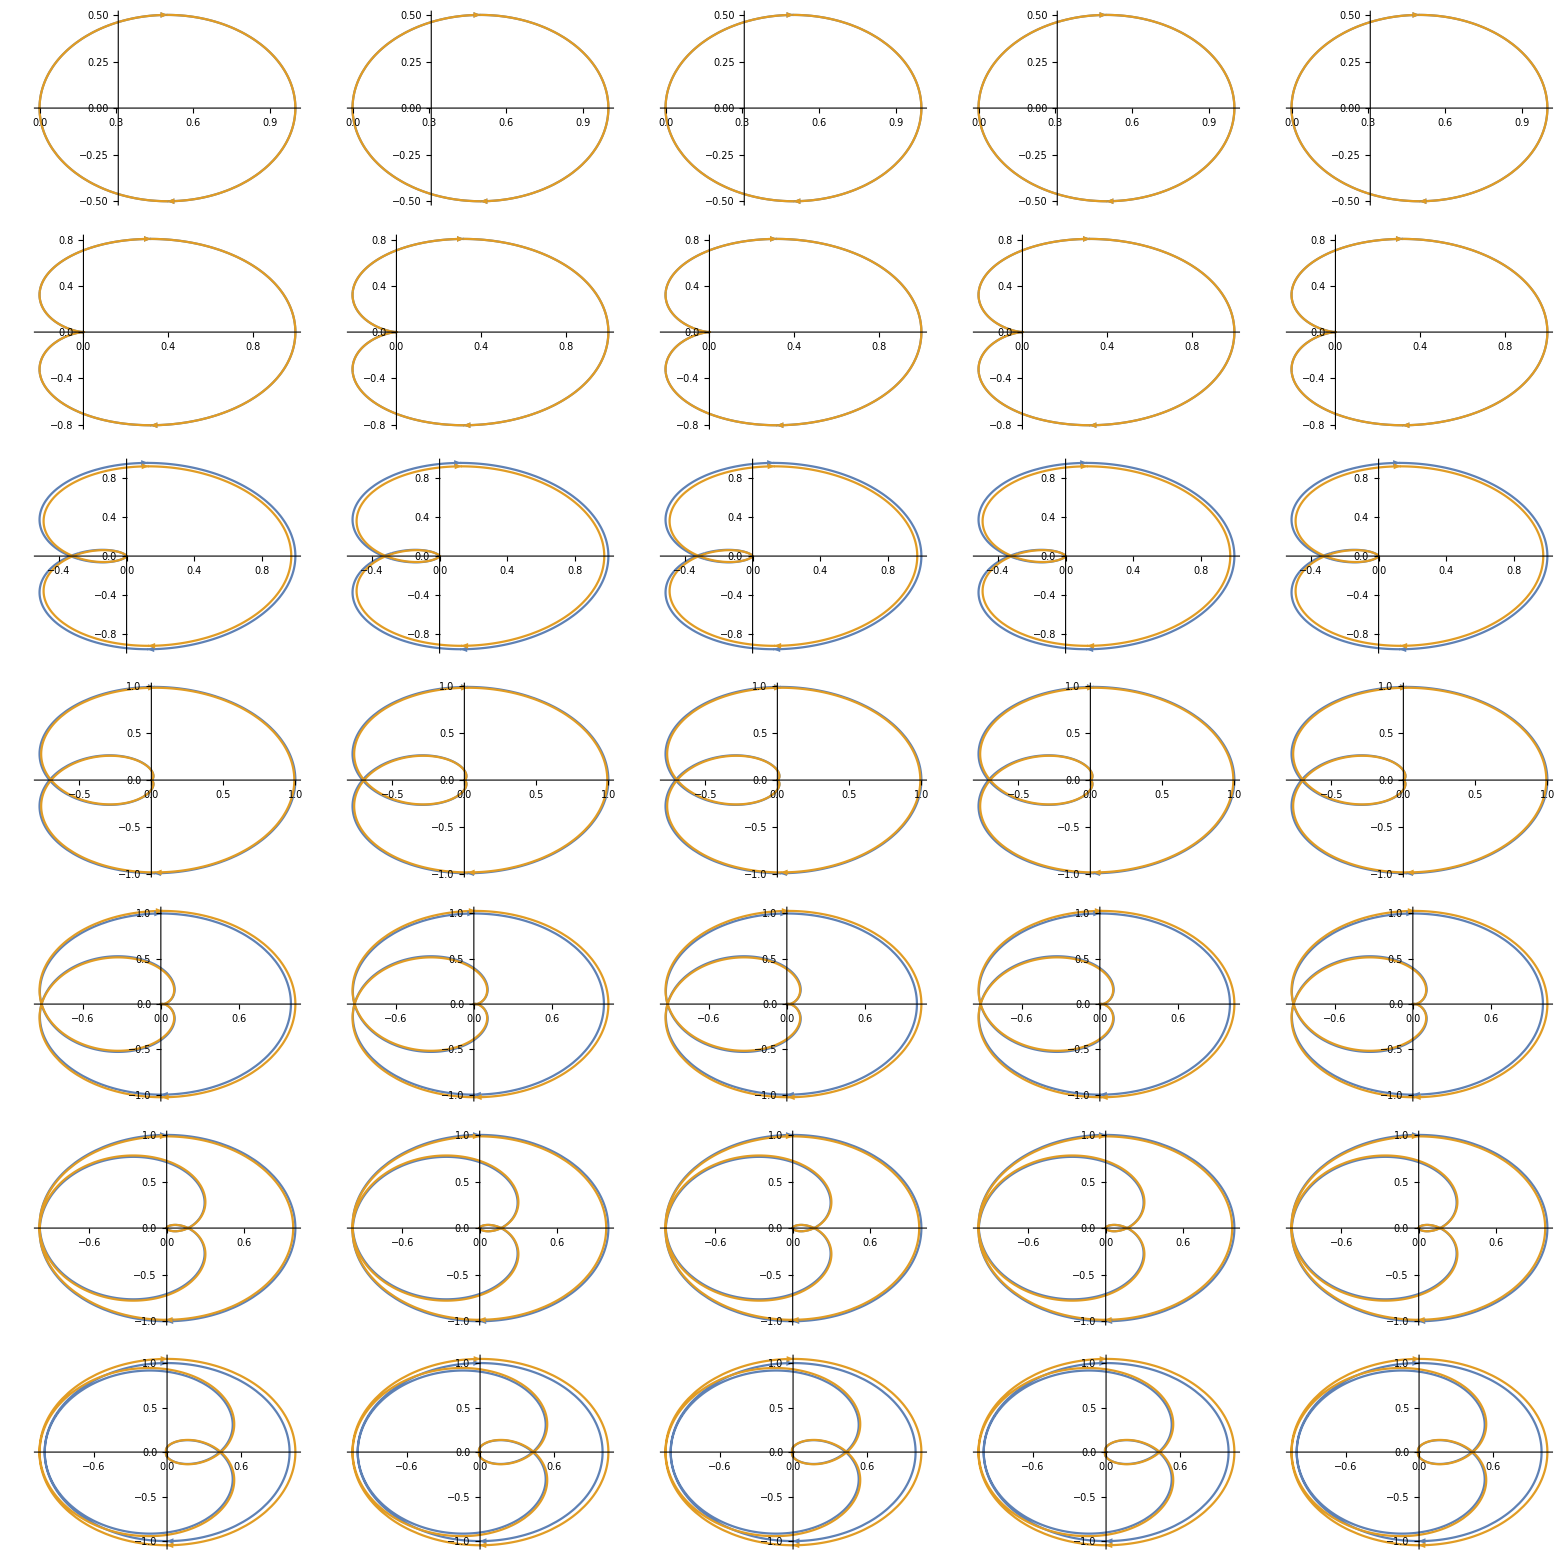

```mathematica
bnyq=Grid@MapThread[NyquistPlot[{#1,#2}]&,{bmodels,bmodelsD},2]
```

### chebyshev

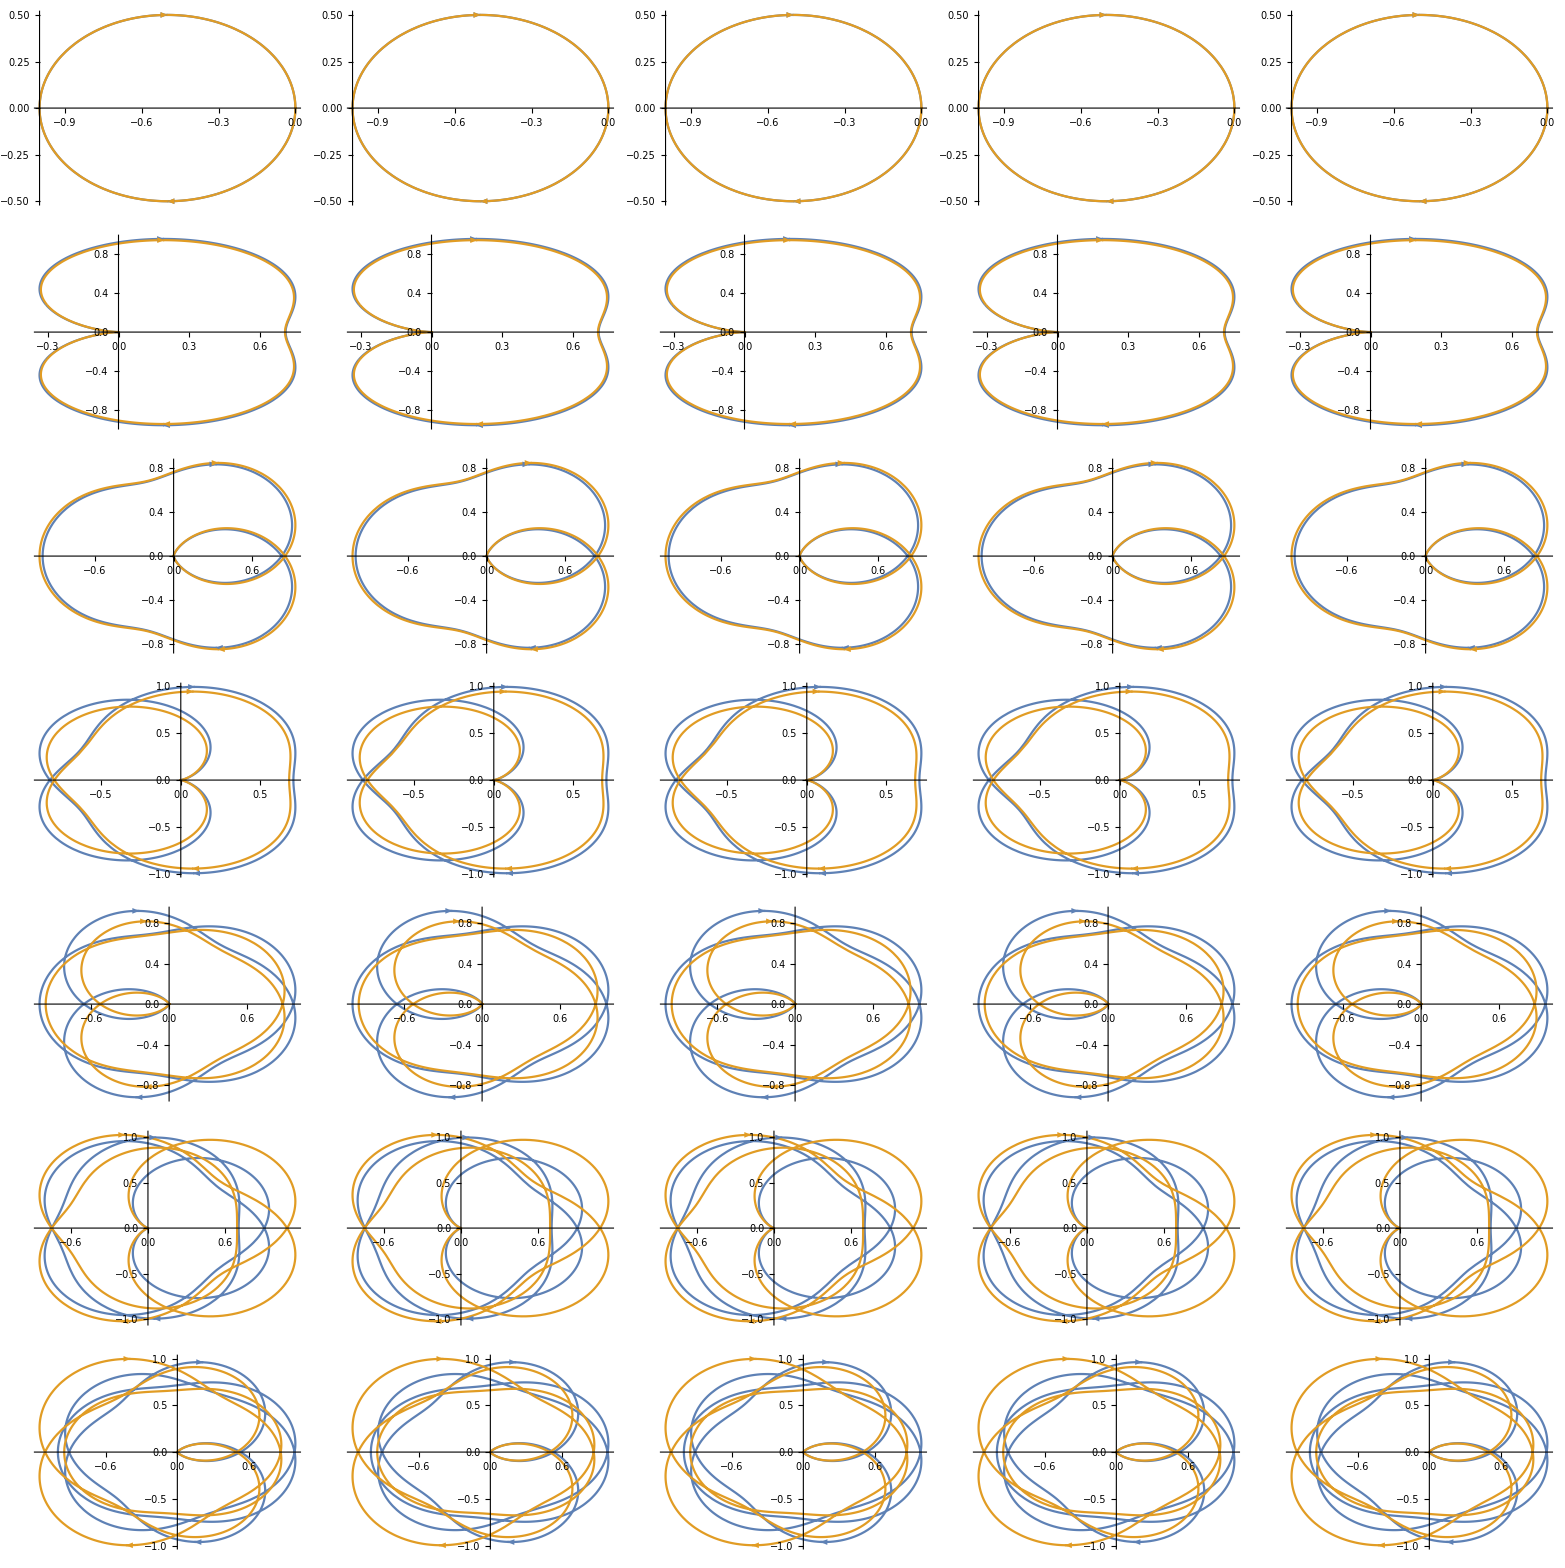

```mathematica
cmodels=Table[Chebyshev1FilterModel[{"Lowpass" ,n,k},s],{n,1,7,1},{k,0.1,0.9,0.2}];
cmodelsD=Map[(DiscretizedModel[#,6])&,cmodels,{2}];
cnyq=Grid@MapThread[NyquistPlot[{#1,#2}]&,{cmodels,cmodelsD},2]
```

### eliptic

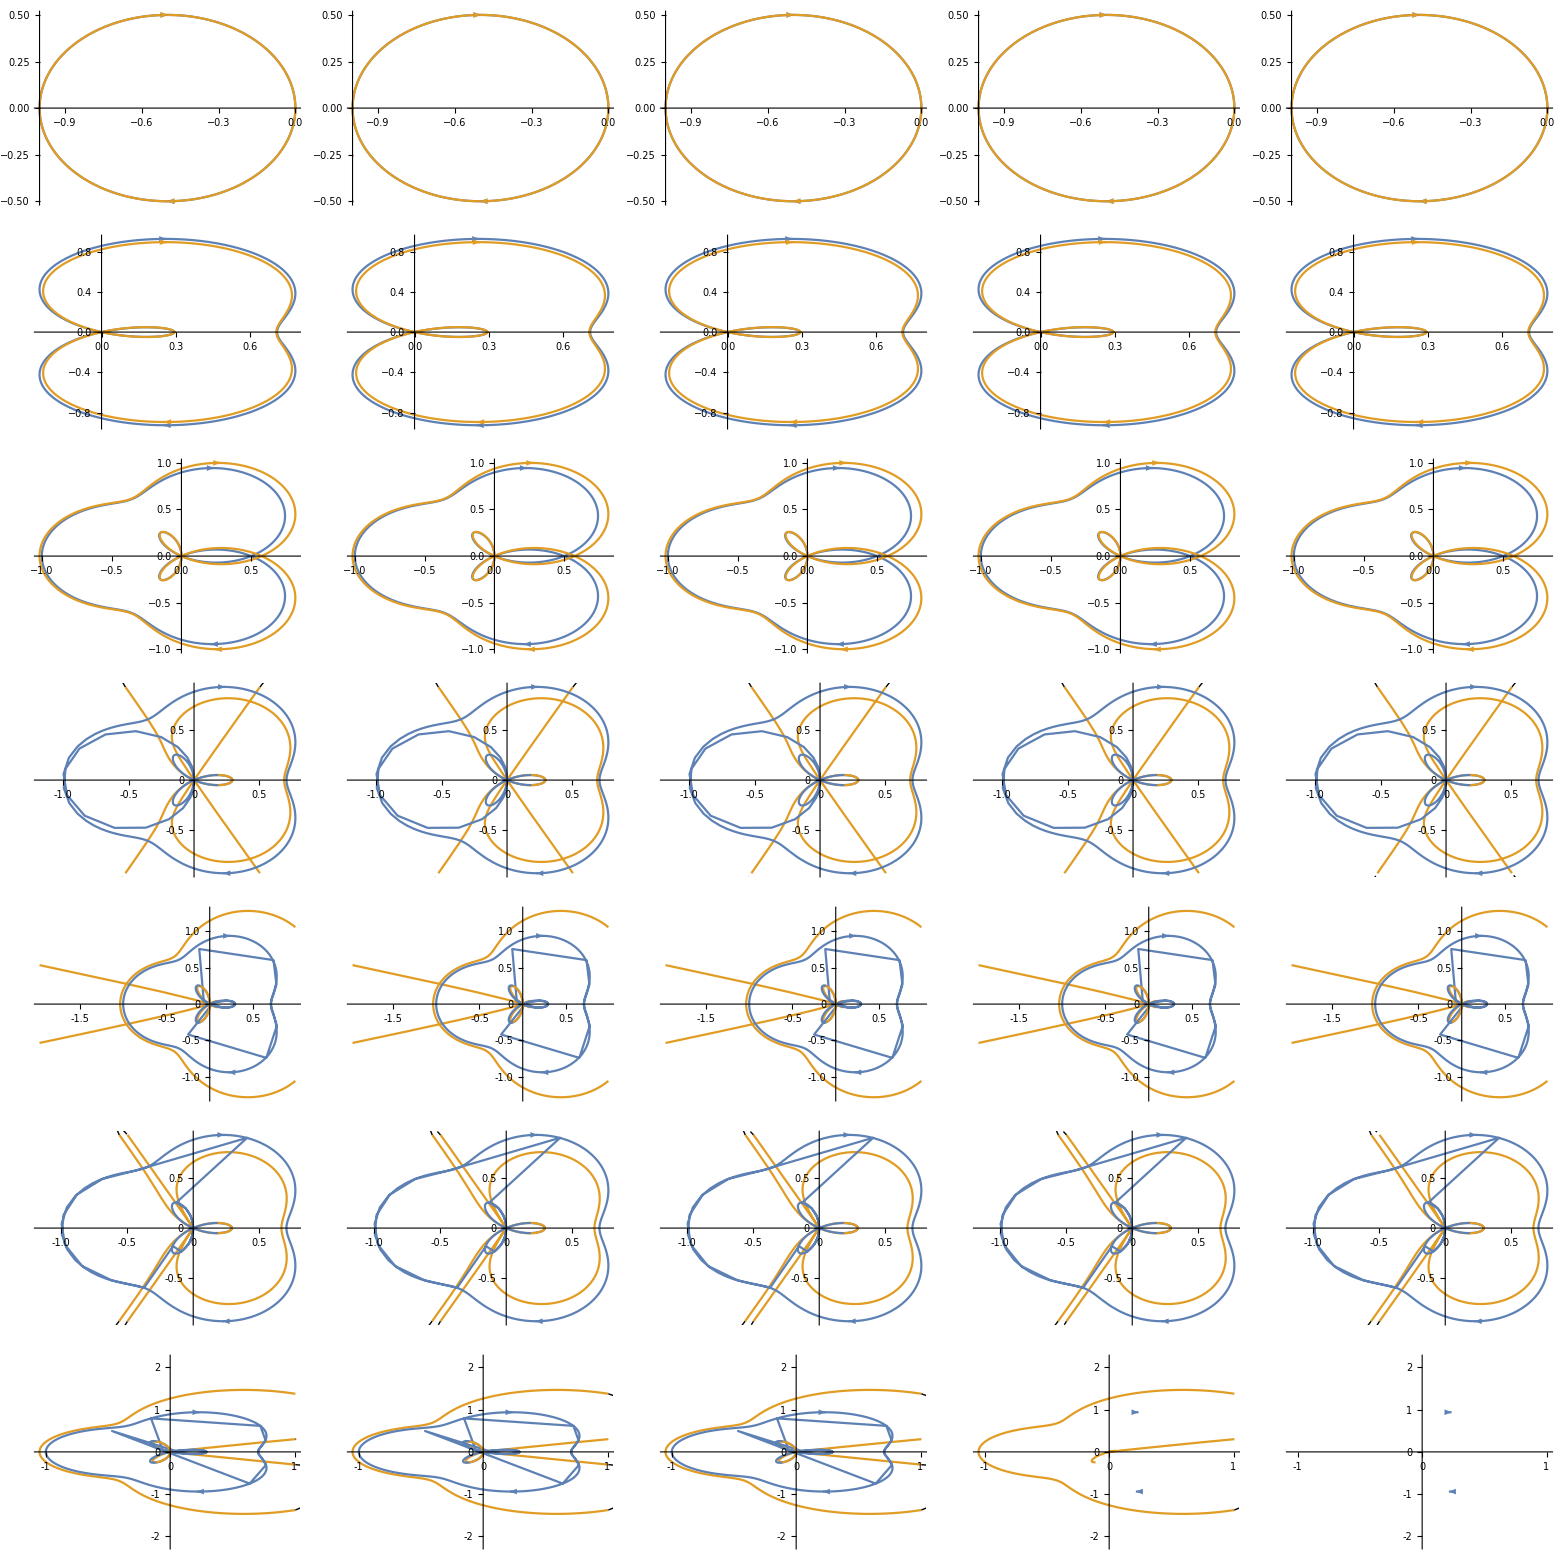

```mathematica
emodels=Table[EllipticFilterModel[{n,k},s],{n,1,7,1},{k,0.1,0.9,0.2}];
emodelsD=Map[(DiscretizedModel[#,6])&,emodels,{2}];
enyq=Grid@MapThread[NyquistPlot[{#1,#2}]&,{emodels,emodelsD},2]
```

## Bode plots

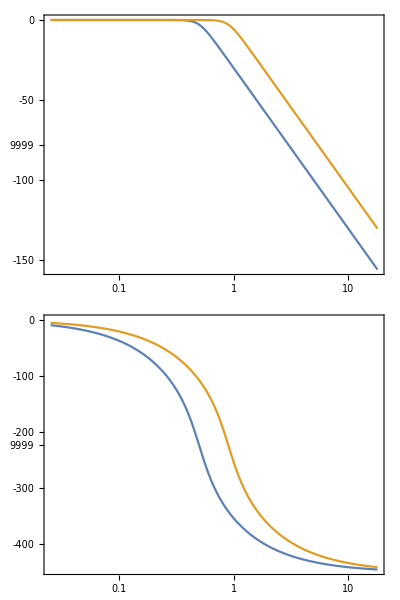

```mathematica
BodePlot[{bmodels[[5,3]],bmodels[[5,5]]}]
```

### Sin

```mathematica
ResponseToSin[ω_,model_,modelD_,NN_,k_]:=Module[{response,responseD},
response=OutputResponse[Rationalize@model[[NN,k]],Sin[ω t],{t,0.01,200}];
responseD=OutputResponse[Rationalize@TransferFunctionModel[modelD[[NN,k]],s],Sin[ω t],{t,0.01,200}];
Plot[{response,responseD},{t,0.1,200},PlotRange->Full]
];
```

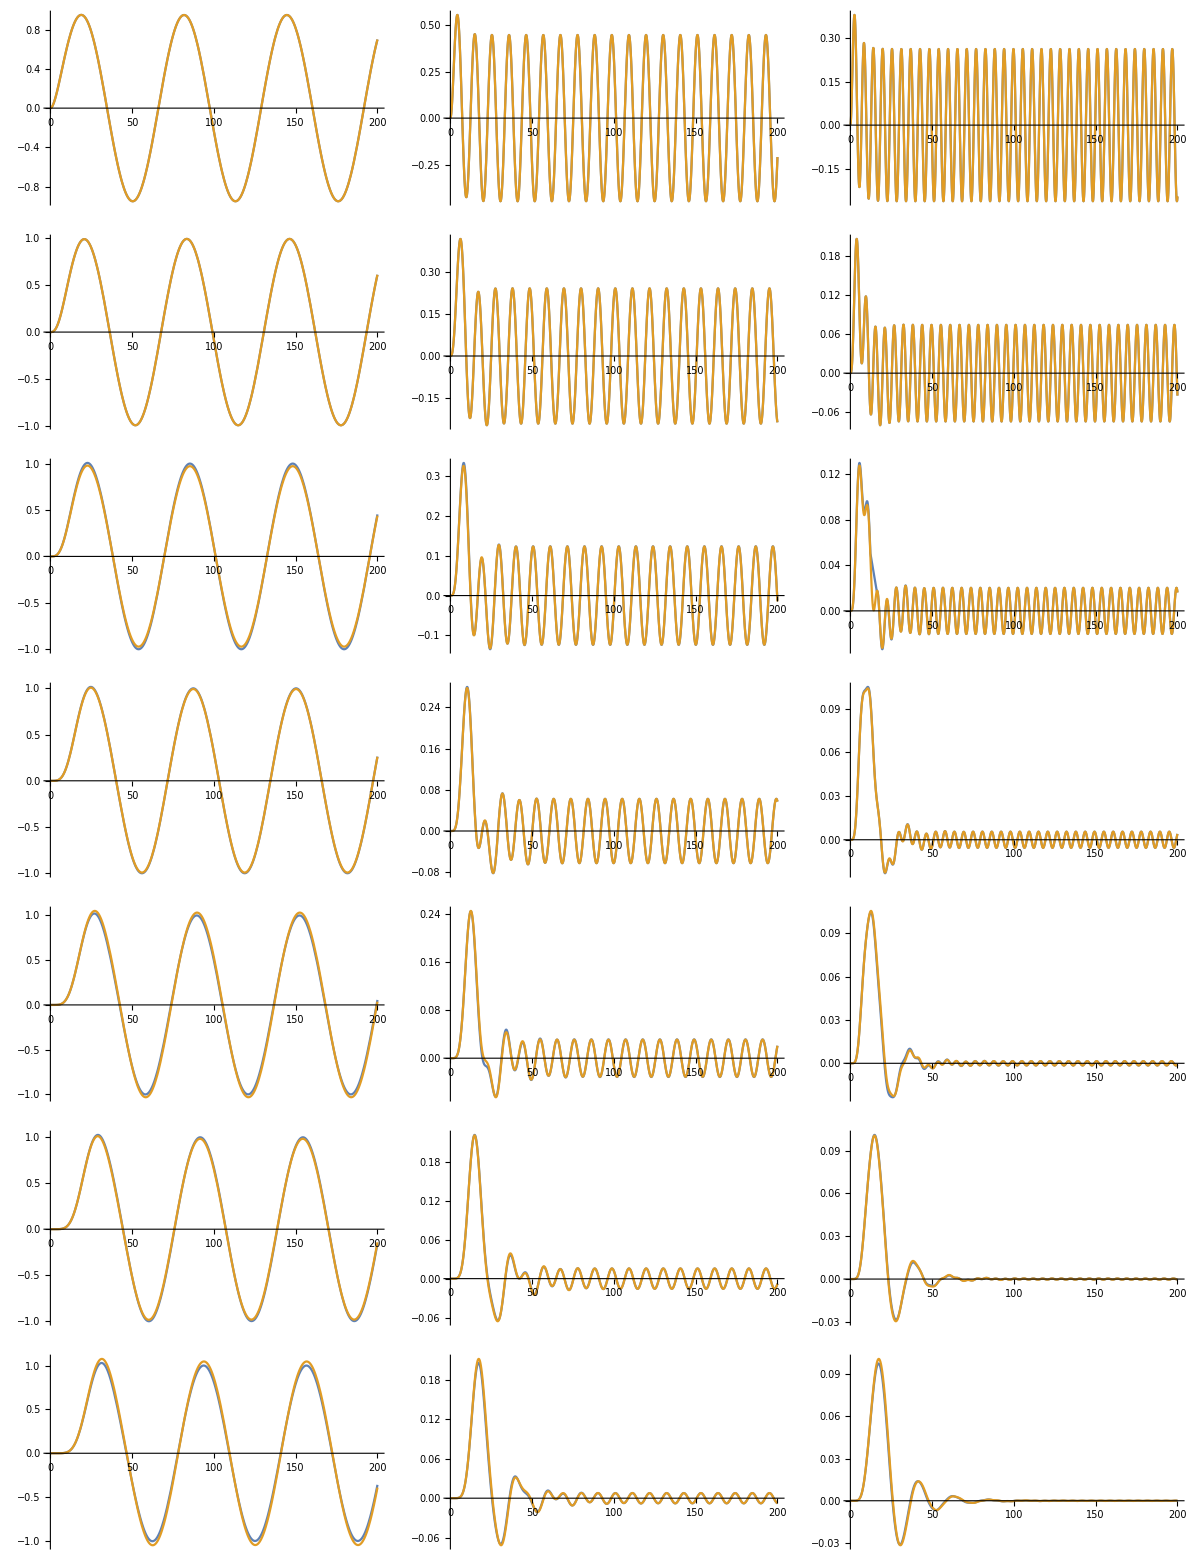

```mathematica
Grid@Table[Table[ResponseToSin[ω,bmodels,bmodelsD,NN,2],{ω,0.1,1.1,0.5}],{NN,1,7}]
```

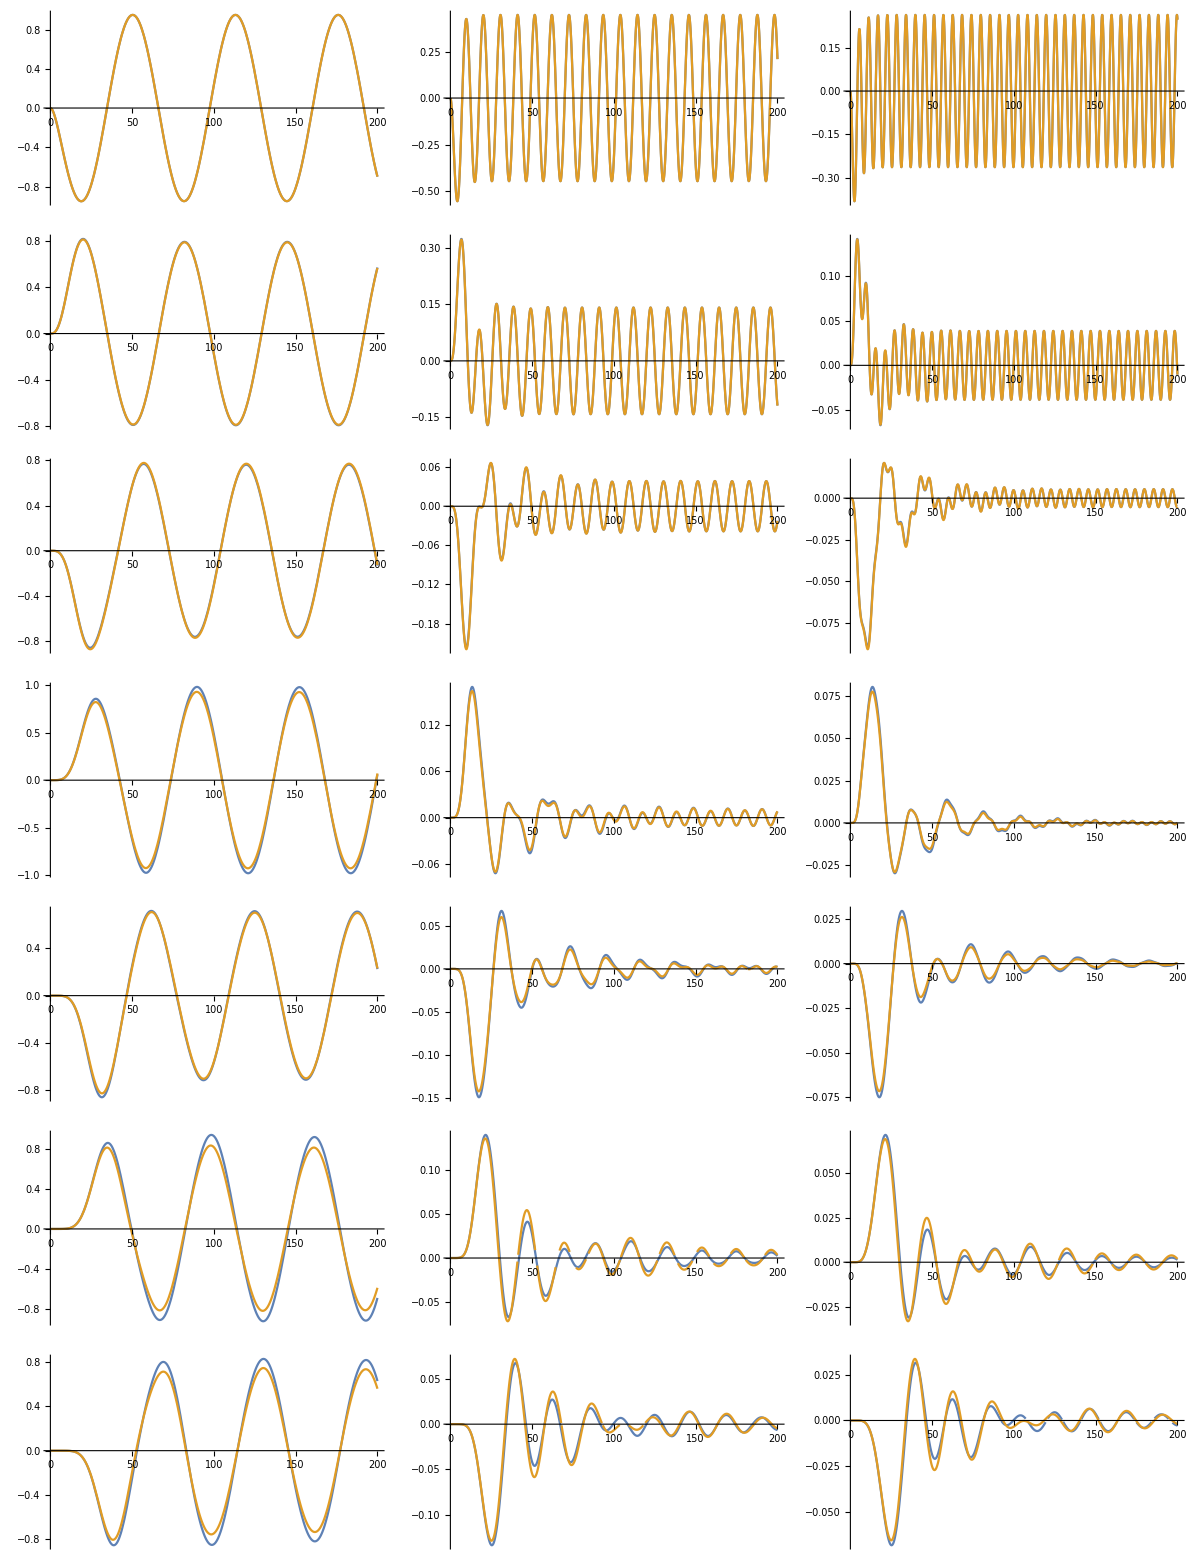

```mathematica
Grid@Table[Table[ResponseToSin[ω,cmodels,cmodelsD,NN,2],{ω,0.1,1.1,0.5}],{NN,1,7}]
```

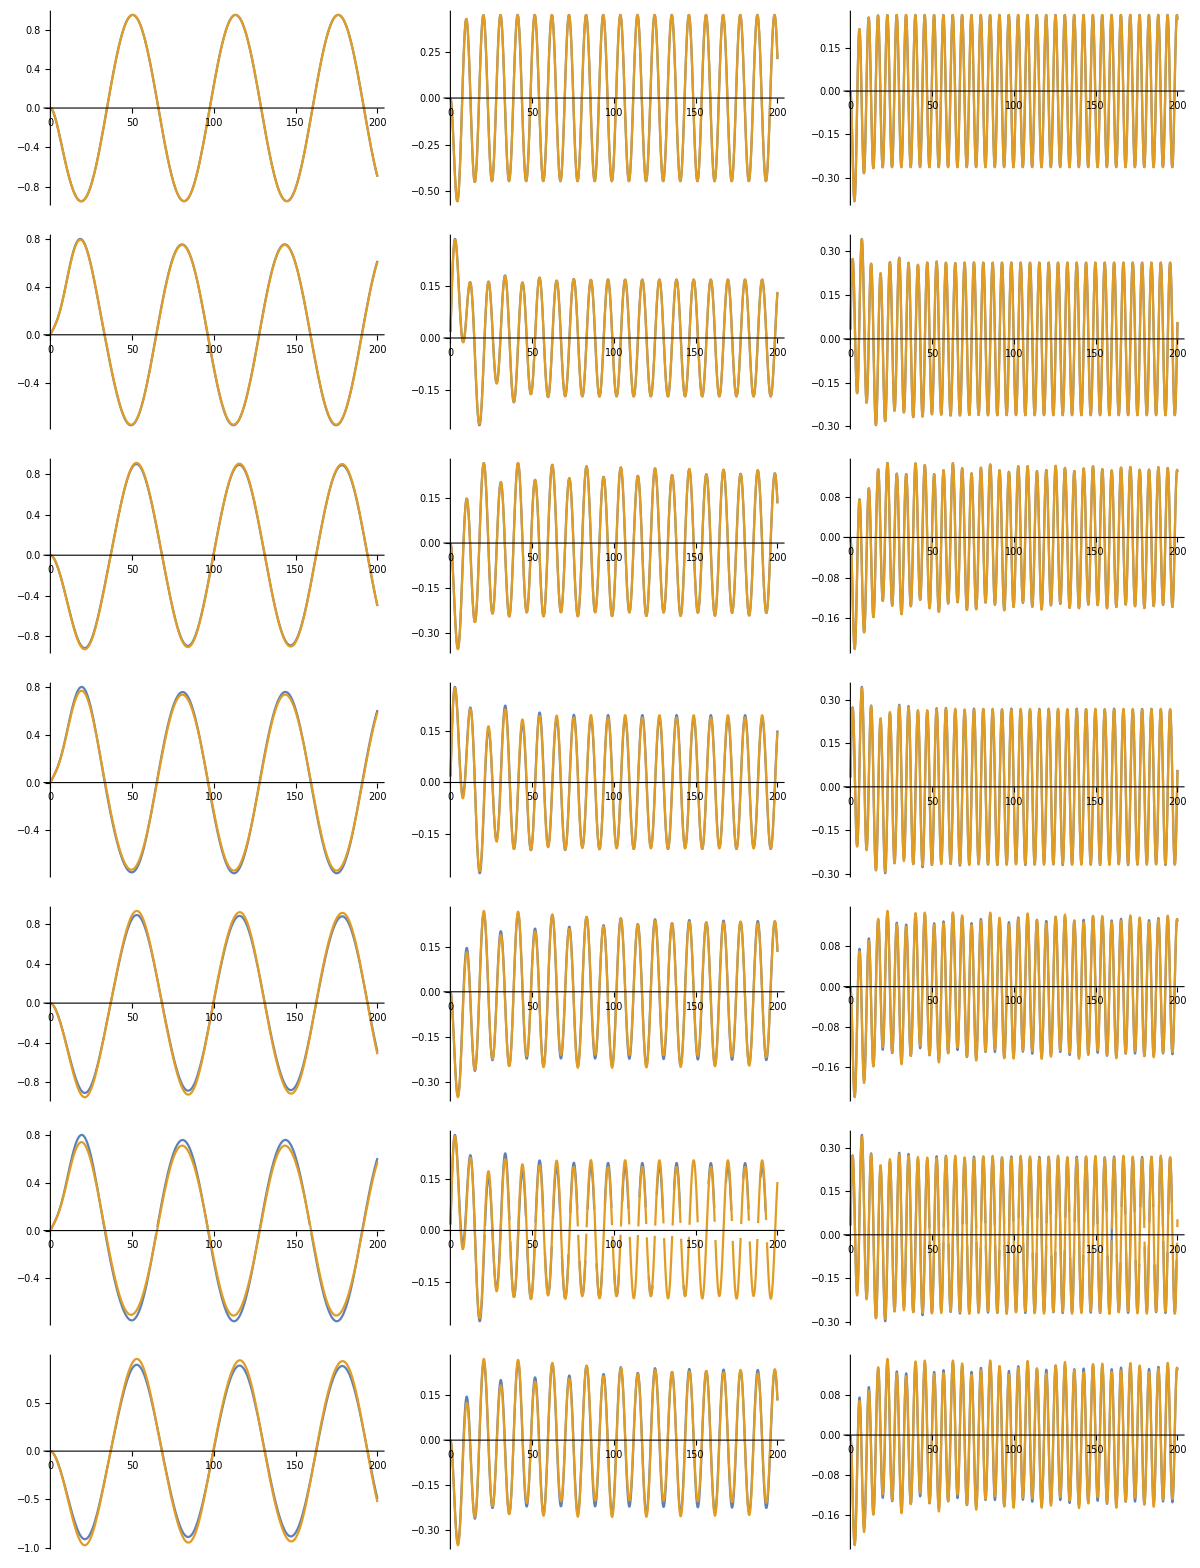

```mathematica
Grid@Table[Table[ResponseToSin[ω,emodels,emodelsD,NN,2],{ω,0.1,1.1,0.5}],{NN,1,7}]
```

```mathematica
ResponseToUnitStep[ω_,model_,modelD_,NN_,k_]:=Module[{response,responseD},
response=OutputResponse[Rationalize@model[[NN,k]],UnitStep[t],{t,0.01,200}];
responseD=OutputResponse[Rationalize@TransferFunctionModel[modelD[[NN,k]],s],UnitStep[t],{t,0.01,200}];
Plot[{response,responseD},{t,0.1,200},PlotRange->Full]
];
```

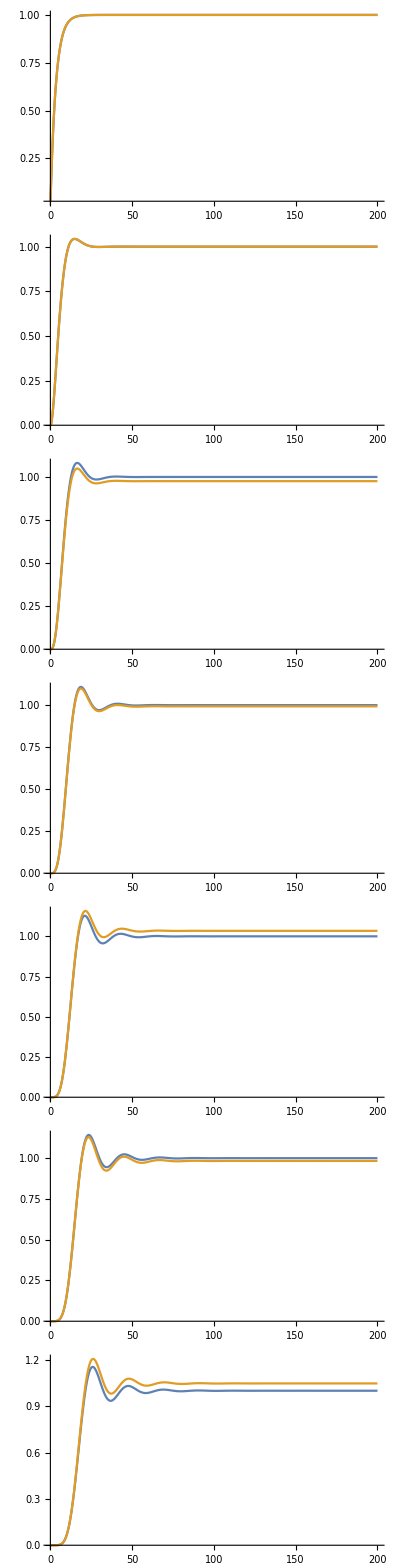

```mathematica
Grid@Table[Table[ResponseToUnitStep[ω,bmodels,bmodelsD,NN,2],{ω,1,1,0.5}],{NN,1,7}]
```

```mathematica
Grid@Table[Table[ResponseToUnitStep[ω,cmodels,cmodelsD,NN,2],{ω,1,1,0.5}],{NN,1,7}]
```

-Graphics-

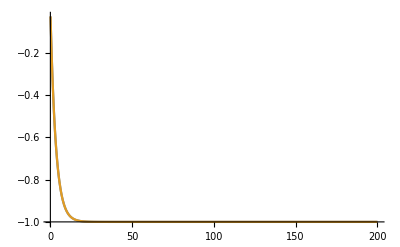
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Grid@Table[Table[ResponseToUnitStep[ω,emodels,emodelsD,NN,2],{ω,1,1,1}],{NN,1,7}]
```

```mathematica
Plot3D[Evaluate[OutputResponse[bmodels[[1,1]],Sin[ω t],t]],{ω,0,π},{t,0,20},AxesLabel->{"ω",t,"y(t)"},MeshFunctions->{#1&},PlotRange->All]
```

-Graphics3D-

```mathematica
bmodels[[7,1]]
```

```mathematica
(1.0000000000000005*^-7)/(((0.02225209339563144-0.09749279121818237 ⅈ)+s) ((0.02225209339563144+0.09749279121818237 ⅈ)+s) ((0.06234898018587335-0.07818314824680299 ⅈ)+s) ((0.06234898018587335+0.07818314824680299 ⅈ)+s) ((0.09009688679024191-0.04338837391175582 ⅈ)+s) ((0.09009688679024191+0.04338837391175582 ⅈ)+s) (0.1+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s111.0000000000000005e-70.022252093395631441FalseFalseFalseAutomaticNoneAutomatic
```

```mathematica
Grid@Table[Table[ResponseToSin[ω,bmodels,bmodelsD,NN,1],{ω,0.0655,0.0659,0.0001}],{NN,7,7}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TransferFunctionPoles@bmodels[[7,1]]//N
TransferFunctionPoles@TransferFunctionModel[bmodelsD[[7,1]],s]//N
```

{{{-0.1,-0.0900969-0.0433884 ⅈ,-0.0900969+0.0433884 ⅈ,-0.062349-0.0781831 ⅈ,-0.062349+0.0781831 ⅈ,-0.0222521-0.0974928 ⅈ,-0.0222521+0.0974928 ⅈ}}}

{{{-0.1+0. ⅈ,-0.0903226-0.0419355 ⅈ,-0.0903226+0.0419355 ⅈ,-0.0612903-0.0774194 ⅈ,-0.0612903+0.0774194 ⅈ,-0.0225806-0.0967742 ⅈ,-0.0225806+0.0967742 ⅈ}}}

```mathematica
TransferFunctionPoles@SystemsModelFeedbackConnect[bmodels[[7,1]]]//N
TransferFunctionPoles@SystemsModelFeedbackConnect[TransferFunctionModel[bmodelsD[[7,1]],s]]//N
```

{{{-0.150401,-0.114182-0.0867741 ⅈ,-0.114182+0.0867741 ⅈ,-0.0352906+0.117271 ⅈ,-0.0352906-0.117271 ⅈ,-0.0000249042-0.0656578 ⅈ,-0.0000249042+0.0656578 ⅈ}}}

{{{-0.150887,-0.114246+0.0862225 ⅈ,-0.114246-0.0862225 ⅈ,-0.0352183+0.117063 ⅈ,-0.0352183-0.117063 ⅈ,0.000713988+0.0650482 ⅈ,0.000713988-0.0650482 ⅈ}}}

```mathematica
response=OutputResponse[Rationalize@emodels[[2,5]],UnitStep[t],{t,0.0,1000}];
responseD=OutputResponse[Rationalize@TransferFunctionModel[emodelsD[[2,5]],s],UnitStep[t],{t,0,1000}];
Plot[{response,responseD},{t,0,1000},PlotRange->Full]
```

-Graphics-

-Graphics-

```mathematica
AsymptoticallyStableQ[tfm_?ContinuousTimeModelQ]:=If[
Count[TransferFunctionPoles[tfm],Complex[x_?NonNegative,_]|x_?NonNegative,{3}]>0,False,True]
```

```mathematica
AsymptoticallyStableQ[tfm_?DiscreteTimeModelQ]:=If[
Count[TransferFunctionPoles[tfm],_?(Abs[#]≥1&),{3}]>0,False,True]
```

```mathematica
bstable=Grid@MapThread[If[AsymptoticallyStableQ[#1],"[S,", "[NS,"]<>If[AsymptoticallyStableQ[TransferFunctionModel[#2,s]],"S]","NS]"]&,{bmodels,bmodelsD},2]
```

[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]

```mathematica
cstable=Grid@MapThread[If[AsymptoticallyStableQ[#1],"[S,", "[NS,"]<>If[AsymptoticallyStableQ[TransferFunctionModel[#2,s]],"S]","NS]"]&,{cmodels,cmodelsD},2]
```

[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]

```mathematica
estable=Grid@MapThread[If[AsymptoticallyStableQ[#1],"[S,", "[NS,"]<>If[AsymptoticallyStableQ[TransferFunctionModel[#2,s]],"S]","NS]"]&,{emodels,emodelsD},2]
```

[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,NS] | [S,NS] | [S,NS] | [S,NS] | [S,NS]
[S,NS] | [S,NS] | [S,NS] | [S,NS] | [S,NS]
[S,NS] | [S,NS] | [S,NS] | [S,NS] | [S,NS]
[S,NS] | [S,NS] | [S,NS] | [S,NS] | [S,NS]

## Inna ilość bitów

```mathematica
cmodels5D=Map[(DiscretizedModel[#,5])&,cmodels,{2}];
```

```mathematica
bstable=Grid@MapThread[If[AsymptoticallyStableQ[#1],"[S,", "[NS,"]<>If[AsymptoticallyStableQ[TransferFunctionModel[#2,s]],"S]","NS]"]&,{cmodels,cmodels5D},2]
```

[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,S] | [S,S] | [S,S] | [S,S] | [S,S]
[S,NS] | [S,NS] | [S,NS] | [S,NS] | [S,NS]

```mathematica
bmodels=Table[ButterworthFilterModel[{"Lowpass" ,n,k},s],{n,1,7,1},{k,0.1,0.9,0.2}];
bmodelsD=Map[(DiscretizedModel[#,6])&,bmodels,{2}];
```

```mathematica
ToDiscreteTimeModel[bmodels[[1,1]],1,z]
```

(0.1 (1.+1. z))/(-1.9+2.1 z)1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z110.1-1.90000000000000011FalseFalseFalseAutomaticNoneAutomatic

```mathematica
bnyq=Grid@MapThread[NyquistPlot[{#1,#2}]&,{bmodels,bmodelsD},2]
```

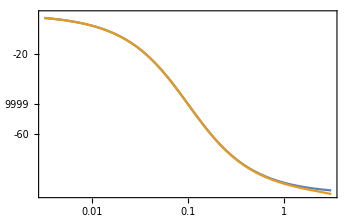
-Graphics-
-Graphics-

```mathematica
BodePlot[{bmodels[[1,1]],ToDiscreteTimeModel[bmodels[[1,1]],1,z]}]
```

## Analiza współczynników filtrów

```mathematica
Manipulate[Column[{TransferFunctionFactor@Chop@filter[{n,ω},s],TransferFunctionFactor@ToDiscreteTimeModel[Chop@filter[{n,ω},s],1]}],{{n,2,"filter order"},2,8,1,Appearance->"Labeled"},
{{ω,1,"filter freq"},0,π,Appearance->"Labeled"},
{{filter,ButterworthFilterModel},{ButterworthFilterModel->"Butterworth",Chebyshev1FilterModel->"Chebyshev 1",Chebyshev2FilterModel->"Chebyshev 2",EllipticFilterModel->"elliptic"}},SaveDefinitions->True]
```

## Filtry cyfrowe

### butter

```mathematica
bmodels=Table[ButterworthFilterModel[{"Lowpass" ,n,k},s],{n,1,7,1},{k,0.1,0.9,0.2}];
DGbmodels=Table[ToDiscreteTimeModel[ButterworthFilterModel[{"Lowpass" ,n,k},s],1],{n,1,7,1},{k,0.1,0.9,0.2}];
bmodelsD=Map[(DiscretizedModel[#,6])&,bmodels,{2}];
```

```mathematica
Chop@bmodels[[1,1]]
tf=TransferFunctionFactor[ToDiscreteTimeModel[bmodels[[1,1]],1]]
```

0.1/(0.1+s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s110.10.11FalseFalseFalseAutomaticNoneAutomatic

(0.047619 (1.+z))/(-0.904762+z)1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#z110.047619047619047616-0.90476190476190471FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Plot[Abs[DiscretizedModel[DGbmodels[[5,5]],6]/.{s->ⅇ^ⅈω}],{ω,0,π},AxesLabel->{ω,None},GridLines->Automatic,PlotRange->Full,AspectRatio->1/3]
```

-Graphics-

### cheby

```mathematica
cmodels=Table[Chebyshev1FilterModel[{"Lowpass" ,n,k},s],{n,1,7,1},{k,0.1,0.9,0.2}];
cmodelsD=Map[(DiscretizedModel[#,6])&,cmodels,{2}];
```

```mathematica
cnyq=Grid@MapThread[NyquistPlot[{#1,#2}]&,{cmodels,cmodelsD},2]
```

### eliptic

```mathematica
emodels=Table[EllipticFilterModel[{n,k},s],{n,1,7,1},{k,0.1,0.9,0.2}];
emodelsD=Map[(DiscretizedModel[#,6])&,emodels,{2}];
```

```mathematica
enyq=Grid@MapThread[NyquistPlot[{ToContinuousTimeModel@#1,#2}]&,{emodels,emodelsD},2]
```

$Aborted

```mathematica
NyquistPlot[ToDiscreteTimeModel[emodels[[2,2]],1]]
```

-Graphics-

```mathematica
Factor[TransferFunctionFactor[ToDiscreteTimeModel[emodels[[2,2]],1]][z][[1,1]]]
```

(0.282117 ((-0.908442+0.418012 ⅈ)+1. z) ((-0.908442-0.418012 ⅈ)+1. z))/(((-0.900849-0.251452 ⅈ)+1. z) ((-0.900849+0.251452 ⅈ)+1. z))

```mathematica
Factor@DiscretizeModel[ToDiscreteTimeModel[emodels[[2,2]],1],24]
```

(1.22778 (-1.32645+1. z) (-1.32645+1. z))/(-1.1523+1. z)^2

```mathematica
Denominator@ToDiscreteTimeModel[emodels[[2,2]],1][z][[1,1]]
```

3.80696-7.84102 z+4.35202 z^2

```mathematica
tf=TransferFunctionFactor@ToDiscreteTimeModel[emodels[[2,2]],1]
TransferFunctionPoles[tf]
TransferFunctionZeros[tf]
tf[0]
```

(0.282117 ((-0.908442-0.418012 ⅈ)+z) ((-0.908442+0.418012 ⅈ)+z))/(((-0.900849-0.251452 ⅈ)+z) ((-0.900849+0.251452 ⅈ)+z))1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#z110.28211740025119475-0.90084943755545291FalseFalseFalseAutomaticNoneAutomatic

{{{0.900849-0.251452 ⅈ,0.900849+0.251452 ⅈ}}}

{{{0.908442-0.418012 ⅈ,0.908442+0.418012 ⅈ}}}

{{0.322509+1.58647×10^-17 ⅈ}}

## Badanie stabilności filtrów cyfrowych (6 bit)

### Ustalenie postaci filtrów cyfrowych

Poniżej znajdują się definicje filtrów analogowych i ich cyfrowych odpowiedników w postaci tabel dla rzędu N={1,2,...7} oraz częstości ω={ωmin, ωmax, Δω}

#### Definicje

```mathematica
Δω=0.3;
ωmin=0.1;
ωmax=2.0;
```

#### Butterworth

```mathematica
bmodels=Table[TransferFunctionFactor@ButterworthFilterModel[{"Lowpass" ,n,ω},s],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
DGbmodels=Table[TransferFunctionFactor@ToDiscreteTimeModel[ButterworthFilterModel[{"Lowpass" ,n,ω},s],1],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
```

#### Chebyshev 1

```mathematica
c1models=Table[TransferFunctionFactor@Chebyshev1FilterModel[{"Lowpass" ,n,ω},s],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
DGc1models=Table[TransferFunctionFactor@ToDiscreteTimeModel[Chebyshev1FilterModel[{"Lowpass" ,n,ω},s],1],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
```

#### Chebyshev 2

```mathematica
c2models=Table[TransferFunctionFactor@Chebyshev2FilterModel[{n,ω},s],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
DGc2models=Table[TransferFunctionFactor@ToDiscreteTimeModel[Chebyshev2FilterModel[{n,ω},s],1],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
```

#### Eliptic

```mathematica
emodels=Table[TransferFunctionFactor@EllipticFilterModel[{n,ω},s],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
DGemodels=Table[TransferFunctionFactor@ToDiscreteTimeModel[EllipticFilterModel[{n,ω},s],1],{n,1,7,1},{ω,ωmin,ωmax,Δω}];
```

### Dyskretyzacja na poziomie zer i biegunów

#### Wstęp

Na początek przedstawiam sposób w jaki dyskretyzowałem dotychczas, tj. mając filtr cyfrowy w postaci (a_0(z-a_1))/((z-b_1)(z-b_2)) dyskretyzowałem liczby a_1,b_1, b_2.
Okazuje się, że nie jest najlepszy sposób dyskretyzacji by sprawdzić rzeczywiste efekty tego procesu. Lepszy sposób prezentowany w kolejnym paragrafie, polega na dyskretyzacji końcowych współczynników filtru, a więc współczynników c_0,c_1,d_0, d_1, d_2 filtru (c_0+c_1 z)/(d_0+d_1 z+d_2 z^2)  będącego wymnożoną postacią wyżej przedstawionego filtru.

#### Definicje

```mathematica
DiscretizeList[x_,max_,bits_]:=If[ #≥0 ,1,-1]Round[(Abs[#]/max)(Power[2,bits-1]-1)] max/(Power[2,bits-1]-1) &/@x;
```

```mathematica
DiscretizeComplexLists[x_,y_,coeff_,bits_]:=Module[{xD,yD,coeffD,max},
If[y=={},{},
max=Max[Abs[Join[Re@x,Im@x,Re@y,Im@y,Re@{coeff},Im@{coeff}]]];
xD=DiscretizeList[Re@x,max,bits]+ⅈ DiscretizeList[Im@x,max,bits];
yD=DiscretizeList[Re@y,max,bits]+ⅈ DiscretizeList[Im@y,max,bits];
coeffD=Total[DiscretizeList[{Re@coeff,ⅈ Im@coeff},max,bits]];
{xD,yD,coeffD}]
];
DiscretizeModel[tf_,bits_]:=Module[{tfD,coeff,zeros,poles,coeffD,zerosD,polesD},
coeff=First[Flatten[Numerator[tf[z]]]];
coeff=If[Length[coeff]>0,coeff[[1]],coeff];
zeros=(z/.Solve[Numerator@(tf[z])==0,z])/.{z->{}};
poles=(z/.Solve[Denominator@(tf[z]/coeff)==0,z]);
{zerosD,polesD,coeffD}=DiscretizeComplexLists[zeros,poles,Last@poles,bits];
(*nie wykorzystuję coeffD, bo często jest bardzo mały i przechodzi w 0 podczas dyskretyzacji, by nie zaburzyć wyniku, podają mu inny, istniejący biegun*)
	Chop[coeff (z-zerosD/.{List->Times})/(z-polesD/.{List->Times})]
];
```

Pomocnicza funkcja by pobrać bieguny zdyskretyzowanych filtrów

```mathematica
ExtractPoles[tf_]:=Module[{coeff},
coeff=First[Flatten[Numerator[tf]]];
coeff=If[Length[coeff]>0,coeff[[1]],coeff];
(z/.Solve[Denominator@(tf/coeff)==0,z])
]
```

Ustalamy ilość bitów do symulacji

```mathematica
bity=6;
```

#### Testy

```mathematica
{a,b,c}=DiscretizeComplexLists[{1,2,3},{ⅈ,ⅈ 2,ⅈ 3},2,6]
```

{{30/31,63/31,3},{(30 ⅈ)/31,(63 ⅈ)/31,3 ⅈ},63/31}

Dyskretyzujemy na poziomie filtrów cyfrowych

```mathematica
buttModel=DGbmodels[[1,1]]
```

(0.047619 (1.+z))/(-0.904762+z)1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#z110.047619047619047616-0.90476190476190471FalseFalseFalseAutomaticNoneAutomatic

```mathematica
polesButt=TransferFunctionPoles[buttModel][[1,1]]
```

{0.904762}

```mathematica
buttModelD=DiscretizeModel[buttModel,bity]
```

(0.047619 (1.+z))/(-0.903226+z)

```mathematica
polesButtD=ExtractPoles[buttModelD]
```

{0.90411}

Ale funkcja dyskretyzująca działa też dla filtrów analogowych

```mathematica
buttModel2=bmodels[[3,3]]
```

0.125/(((0.25-0.433013 ⅈ)+s) ((0.25+0.433013 ⅈ)+s) (0.5+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s110.1250.251FalseFalseFalseAutomaticNoneAutomatic

```mathematica
buttModel2D=DiscretizeModel[buttModel2,bity]
```

0.125/(((0.258065-0.435484 ⅈ)+z) ((0.258065+0.435484 ⅈ)+z) (0.5+z))

#### Dyskretyzacja

```mathematica
DGbmodelsD=Map[DiscretizeModel[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsD=Map[DiscretizeModel[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsD=Map[DiscretizeModel[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsD=Map[DiscretizeModel[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Definicje

Przygotowywuję funkcję rysującą bieguny i zaznaczającą na czerwono te w których bieguny filtru zdyskretyzowanego wychodzą poza okrąg jednostkowy.

```mathematica
PlotPoles[poles_,poles2_]:=ListPlot[{Transpose[{Re[poles],Im[poles]}],Transpose[{Re[poles2],Im[poles2]}]},PlotRange->1.2{{-1,1},{-1,1}},PlotStyle->{PointSize[Large]},Background->If[Count[poles2,_?(Abs[#]≥1&),{1}]>0,LightRed,White],PlotMarkers->{Automatic,Medium},AxesOrigin->{0,0},Epilog->{Green,Circle[]},AspectRatio->Automatic]

AsymptoticallyStableQ[tfm_?ContinuousTimeModelQ]:=If[
Count[TransferFunctionPoles[tfm],Complex[x_?NonNegative,_]|x_?NonNegative,{3}]>0,False,True]
AsymptoticallyStableQ[tfm_?DiscreteTimeModelQ]:=If[
Count[TransferFunctionPoles[tfm],_?(Abs[#]≥1&),{3}]>0,False,True]
```

##### Testy

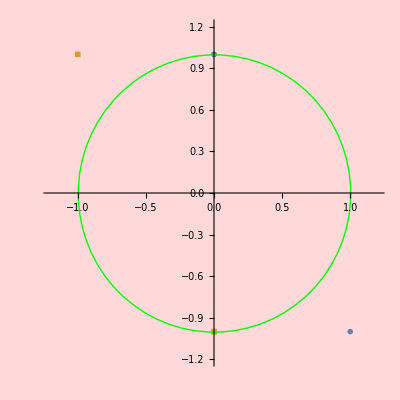

```mathematica
PlotPoles[{1-ⅈ,ⅈ},-{1-ⅈ,ⅈ}]
```

```mathematica
PlotPoles[polesButt,polesButtD]
```

-Graphics-

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsD},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsD},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsD},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsD},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Dyskretyzacja na poziomie współczynników

#### Definicje

```mathematica
DiscretizeList[x_,max_,bits_]:=If[ #≥0 ,1,-1]Round[(Abs[#]/max)(Power[2,bits-1]-1)] max/(Power[2,bits-1]-1) &/@x;
DiscretizeComplexList[x_,y_,bits_]:=Module[{xD,yD,coeffD,max},
If[y=={},{},
max=Max[Abs[Join[Re@x,Im@x,Re@y,Im@y]]];
xD=DiscretizeList[Re@x,max,bits]+ⅈ DiscretizeList[Im@x,max,bits];
yD=DiscretizeList[Re@y,max,bits]+ⅈ DiscretizeList[Im@y,max,bits];
{xD,yD}]
];
DiscretizeModelCoeffs[tf_,bits_]:=Module[{zeros,poles,zerosD,polesD},
	zeros=CoefficientList[Numerator[TransferFunctionExpand[tf][z]][[1,1]],z];
poles=CoefficientList[Denominator[TransferFunctionExpand[tf][z]][[1,1]],z];
{zerosD,polesD}=DiscretizeComplexList[zeros,poles,bits];
	Chop[FromDigits[Reverse[zerosD],z]/(FromDigits[Reverse[polesD],z])]
];
```

#### Testy

```mathematica
{a,c}=DiscretizeComplexList[{1,2,3},{ⅈ,ⅈ 2,ⅈ 3},2]
```

{{0,3,3},{0,3 ⅈ,3 ⅈ}}

Dyskretyzujemy na poziomie filtrów cyfrowych

```mathematica
buttModel=TransferFunctionExpand@DGbmodels[[2,2]]
```

(0.0302379+0.0604758 z+0.0302379 z^2)/((0.572371+0. ⅈ)-(1.45142+0. ⅈ) z+z^2)1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#z110.0302379108436653840.57237136387059961FalseFalseFalseAutomaticNoneAutomatic

```mathematica
polesButt=TransferFunctionPoles[buttModel][[1,1]]
```

{0.72571-0.213814 ⅈ,0.72571+0.213814 ⅈ}

```mathematica
buttModelD=N@DiscretizeModelCoeffs[buttModel,bity]
```

(0.04682+0.04682 z+0.04682 z^2)/(0.56184-1.45142 z+0.98322 z^2)

```mathematica
polesButtD=ExtractPoles[buttModelD]
```

{0.738095-0.16323 ⅈ,0.738095+0.16323 ⅈ}

#### Dyskretyzacja

```mathematica
DGbmodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Dyskusja

Przy dyskretyzacji biegunów koniecznym zabiegiem okazało się nie dyskretyzowanie współczynnika stojącego przed całością filtra, gdyż przy niskich częstotliwościach i wysokich rzędach filtrów stawał się on bardzo mały, a po dyskretyzacji = 0. Przy tych założeniach większość filtrów okazała się stabilna przy dyskretyzacji za pomocą 6 bitów. 
Okazuje się jednak, że dyskretyzacja na poziomie biegunów prowadzi do obniżenia rzędu filtra w przypadku filtrów eliptycznych (tj. zera i bieguny znajdujące się blisko siebie zaczynają wzajemnie się skracać)

Dyskretyzacja współczynników ma bardzo podobny problem widoczny przy niskich częstotliwościach filtru Butterwortha i Chebysheva 1, z powodu znikającego licznika znika cały filtr.
Ponadto widać, iż filtry eliptyczne powyżej 3 rzędu robią się bardzo niestabilne (niektóre nie są zaznaczone na czerwono bo filtr znikł z powodów wspomnianych wyżej)

W świetle tych wyników oraz faktu, iż na urządzeniu będziemy dyskretyzować współczynniki, a nie bieguny, proponuję zastosować dyskretyzację zer i biegunów z osobna, tak by zapobiec zerowaniu się licznika.
Wykonane w celu sprawdzenia tej propozycji symulacje przedstawiam poniżej.

### Dyskretyzacja na poziomie współczynników zer i biegunów z osobna

#### Definicje

Tutaj modyfikuję funkcję DiscretizeComplexList

```mathematica
DiscretizeList[x_,max_,bits_]:=If[ #≥0 ,1,-1]Round[(Abs[#]/max)(Power[2,bits-1]-1)] max/(Power[2,bits-1]-1) &/@x;
DiscretizeComplexList2[x_,y_,bits_]:=Module[{xD,yD,coeffD,max},
If[y=={},{},
max=Max[Abs[Join[Re@x,Im@x]]];
xD=DiscretizeList[Re@x,max,bits]+ⅈ DiscretizeList[Im@x,max,bits];
max=Max[Abs[Join[Re@y,Im@y]]];
yD=DiscretizeList[Re@y,max,bits]+ⅈ DiscretizeList[Im@y,max,bits];
{xD,yD}]
];
DiscretizeModelCoeffs2[tf_,bits_]:=Module[{zeros,poles,zerosD,polesD},
	zeros=CoefficientList[Numerator[TransferFunctionExpand[tf][z]][[1,1]],z];
poles=CoefficientList[Denominator[TransferFunctionExpand[tf][z]][[1,1]],z];
{zerosD,polesD}=DiscretizeComplexList2[zeros,poles,bits];
	Chop[FromDigits[Reverse[zerosD],z]/(FromDigits[Reverse[polesD],z])]
];
```

#### Testy

```mathematica
{a,c}=DiscretizeComplexList[{1,2,3},{ⅈ,ⅈ 2,ⅈ 3},2]
```

{{0,3,3},{0,3 ⅈ,3 ⅈ}}

Dyskretyzujemy na poziomie filtrów cyfrowych

```mathematica
buttModel=TransferFunctionExpand@DGbmodels[[2,2]]
```

(0.0302379+0.0604758 z+0.0302379 z^2)/((0.572371+0. ⅈ)-(1.45142+0. ⅈ) z+z^2)1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#z110.0302379108436653840.57237136387059961FalseFalseFalseAutomaticNoneAutomatic

```mathematica
polesButt=TransferFunctionPoles[buttModel][[1,1]]
```

{0.72571-0.213814 ⅈ,0.72571+0.213814 ⅈ}

```mathematica
buttModelD=N@DiscretizeModelCoeffs[buttModel,bity]
```

(0.04682+0.04682 z+0.04682 z^2)/(0.56184-1.45142 z+0.98322 z^2)

```mathematica
polesButtD=ExtractPoles[buttModelD]
```

{0.738095-0.16323 ⅈ,0.738095+0.16323 ⅈ}

#### Dyskretyzacja

```mathematica
DGbmodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Podsumowanie

Wbrew pozorom podzielenie procesu dyskretyzacji na współczynniki licznika i mianownika nie przyniosło wielkich zmian - filtry który znikały, stały się po prostu niestabilne.
Używając Bode Plot (ilustrujący kwadrat amplitudy (dB) w zależności od ω) można zademonstrować, że lepsze odwzorowanie filtru zależy właśnie od przyjętej strategii dyskretyzacji współczynników.

Poniżej znajdują się przykładowe Bode Ploty dla filtrów Butterwortha trzeciego rzędu i częstości równej 1.

```mathematica
BodePlot[{DGbmodels[[3,3]][ⅇ^(ⅈ ω)],DGbmodelsD[[3,3]]/.{z->ⅇ^(ⅈ ω)},DGbmodelsDc[[3,3]]/.{z->ⅇ^(ⅈ ω)},DGbmodelsDc2[[3,3]]/.{z->ⅇ^(ⅈ ω)}},{ω,0.1,π},PlotLayout->"Magnitude",PlotLegends->{"Idealny","Na poziomie zer i biegunów","Na poziomie współczynników","Na poziomie współczynników (osobno)"},PlotLabel->"Butterworth N=3"]
```

-Graphics-

```mathematica
BodePlot[{DGc1models[[3,3]][ⅇ^(ⅈ ω)],DGc1modelsD[[3,3]]/.{z->ⅇ^(ⅈ ω)},DGc1modelsDc[[3,3]]/.{z->ⅇ^(ⅈ ω)},DGc1modelsDc2[[3,3]]/.{z->ⅇ^(ⅈ ω)}},{ω,0.1,π},PlotLayout->"Magnitude",PlotLegends->{"Idealny","Na poziomie zer i biegunów","Na poziomie współczynników","Na poziomie współczynników (osobno)"},PlotLabel->"Chebyshev 1 N=3"]
```

-Graphics-

```mathematica
BodePlot[{DGc2models[[3,3]][ⅇ^(ⅈ ω)],DGc2modelsD[[3,3]]/.{z->ⅇ^(ⅈ ω)},DGc2modelsDc[[3,3]]/.{z->ⅇ^(ⅈ ω)},DGc2modelsDc2[[3,3]]/.{z->ⅇ^(ⅈ ω)}},{ω,0.1,π},PlotLayout->"Magnitude",PlotLegends->{"Idealny","Na poziomie zer i biegunów","Na poziomie współczynników","Na poziomie współczynników (osobno)"},PlotLabel->"Chebyshev 2 N=3"]
```

-Graphics-

```mathematica
BodePlot[{DGemodels[[3,3]][ⅇ^(ⅈ ω)],DGemodelsD[[3,3]]/.{z->ⅇ^(ⅈ ω)},DGemodelsDc[[3,3]]/.{z->ⅇ^(ⅈ ω)},DGemodelsDc2[[3,3]]/.{z->ⅇ^(ⅈ ω)}},{ω,0.1,π},PlotLayout->"Magnitude",PlotLegends->{"Idealny","Na poziomie zer i biegunów","Na poziomie współczynników","Na poziomie współczynników (osobno)"},PlotLabel->"Chebyshev 1 N=3"]
```

-Graphics-

Jeśli trzeba można wyrysować wszystkie tym poleceniem.

```mathematica
Grid@MapThread[BodePlot[{#1[ⅇ^(ⅈ ω)],#2/.{z->ⅇ^(ⅈ ω)},#3/.{z->ⅇ^(ⅈ ω)},#4/.{z->ⅇ^(ⅈ ω)}},{ω,0.01,π},PlotLayout->"Magnitude"]&,{DGbmodels,DGbmodelsD,DGbmodelsDc,DGbmodelsDc2},2]
```

$Aborted

Wybrana przeze mnie wcześniej procedura dyskretyzacji na poziomie zer i biegunów (dodatkowo wcześniej robiłem to na poziomie filtru analogowego), pomimo swoich pozornych zalet obarczona jest jednak dodatkowym błędem, wynikającym z wymnożenia zdyskretyzowanych zer/biegunów którego należałoby by dokonać nie na liczbach rzeczywistych, lecz na liczbach n-bitowych.
Prawdopodobnie to dyskwalifikuje tę metodę.

Zatem mając dwóch kandydatów (na poziomie współczynników, i na poziomie współczynników - osobno zera i bieguny) do metody dyskretyzacji przeprowadzam symulacje dla wyższej liczby bitów.

## Badanie stabilności filtrów cyfrowych (7 bit)

```mathematica
bity=7;
```

### Dyskretyzacja na poziomie współczynników

#### Dyskretyzacja

```mathematica
DGbmodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Dyskretyzacja na poziomie współczynników zer i biegunów z osobna

#### Dyskretyzacja

```mathematica
DGbmodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Badanie stabilności filtrów cyfrowych (8 bit)

```mathematica
bity=8;
```

### Dyskretyzacja na poziomie współczynników

#### Dyskretyzacja

```mathematica
DGbmodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Dyskretyzacja na poziomie współczynników zer i biegunów z osobna

#### Dyskretyzacja

```mathematica
DGbmodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Badanie stabilności filtrów cyfrowych (9 bit)

```mathematica
bity=9;
```

### Dyskretyzacja na poziomie współczynników

#### Dyskretyzacja

```mathematica
DGbmodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Dyskretyzacja na poziomie współczynników zer i biegunów z osobna

#### Dyskretyzacja

```mathematica
DGbmodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Badanie stabilności filtrów cyfrowych (10 bit)

```mathematica
bity=10;
```

### Dyskretyzacja na poziomie współczynników

#### Dyskretyzacja

```mathematica
DGbmodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Dyskretyzacja na poziomie współczynników zer i biegunów z osobna

#### Dyskretyzacja

```mathematica
DGbmodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Badanie stabilności filtrów cyfrowych (11 bit)

```mathematica
bity=11;
```

### Dyskretyzacja na poziomie współczynników

#### Dyskretyzacja

```mathematica
DGbmodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Dyskretyzacja na poziomie współczynników zer i biegunów z osobna

#### Dyskretyzacja

```mathematica
DGbmodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Badanie stabilności filtrów cyfrowych (12 bit)

```mathematica
bity=12;
```

### Dyskretyzacja na poziomie współczynników

#### Dyskretyzacja

```mathematica
DGbmodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Dyskretyzacja na poziomie współczynników zer i biegunów z osobna

#### Dyskretyzacja

```mathematica
DGbmodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Badanie stabilności filtrów cyfrowych (13 bit)

```mathematica
bity=13;
```

### Dyskretyzacja na poziomie współczynników

#### Dyskretyzacja

```mathematica
DGbmodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Dyskretyzacja na poziomie współczynników zer i biegunów z osobna

#### Dyskretyzacja

```mathematica
DGbmodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Badanie stabilności filtrów cyfrowych (14 bit)

```mathematica
bity=14;
```

### Dyskretyzacja na poziomie współczynników

#### Dyskretyzacja

```mathematica
DGbmodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Dyskretyzacja na poziomie współczynników zer i biegunów z osobna

#### Dyskretyzacja

```mathematica
DGbmodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Badanie stabilności filtrów cyfrowych (15 bit)

```mathematica
bity=15;
```

### Dyskretyzacja na poziomie współczynników

#### Dyskretyzacja

```mathematica
DGbmodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Dyskretyzacja na poziomie współczynników zer i biegunów z osobna

#### Dyskretyzacja

```mathematica
DGbmodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Badanie stabilności filtrów cyfrowych (16 bit)

```mathematica
bity=16;
```

### Dyskretyzacja na poziomie współczynników

#### Dyskretyzacja

```mathematica
DGbmodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc=Map[DiscretizeModelCoeffs[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Dyskretyzacja na poziomie współczynników zer i biegunów z osobna

#### Dyskretyzacja

```mathematica
DGbmodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGbmodels,{2}];
```

```mathematica
DGc1modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc1models,{2}];
```

```mathematica
DGc2modelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGc2models,{2}];
```

```mathematica
DGemodelsDc2=Map[DiscretizeModelCoeffs2[#,bity]&,DGemodels,{2}];
```

#### Porównanie położenia biegunów

##### Butterworth

W prawo rośnie częstotliwość, w dół rośnie rząd filtra.

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGbmodels,DGbmodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 1

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc1models,DGc1modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Chebyshev 2

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGc2models,DGc2modelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

##### Eliptyczne

```mathematica
Grid@MapThread[PlotPoles[TransferFunctionPoles[#1][[1,1]],ExtractPoles[#2]]&,{DGemodels,DGemodelsDc2},2]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Skompresowana wersja

Zdaje sobie sprawę z tego jak fatalnie się to czyta, zwłaszcza bez spisu treści. Dlatego postanowiłem skompresować najważniejsze wyniki.
Poniżej znajduje się wizualizacja stabilności filtrów, zasada jest ta sama - w dół rośnie rząd, w prawo rośnie częstość graniczna.
A teraz mała incepcja - promień pierścienia jest związany z liczbą bitów. Środkowy okrąg jest 5 bitowy, każdy kolejny 3 bity więcej, okręgów jest 9, zatem ostatni okrąg reprezentuje 5+9*3=5+27=32 bity. Kolor niebieski oznacza filtr stabilny, kolor pomarańczowy - niestabilny. Za
Zaczynamy!

```mathematica
SP[p_]:=If[Count[p,_?(Abs[#]≥1&),{1}]>0,Lighter[Orange],LightBlue]
```

```mathematica
StableOrNot[p1_,p2_,p3_,p4_,p5_,p6_,p7_,p8_,p9_]:=Graphics[{SP[p1],Disk[{0,0}],
EdgeForm[Directive[Dashed,Gray]],SP[p2],Disk[{0,0},{0.9,0.9}],
EdgeForm[Directive[Dashed,Gray]],SP[p3],Disk[{0,0},{0.8,0.8}],
EdgeForm[Directive[Dashed,Gray]],SP[p4],Disk[{0,0},{0.7,0.7}],
EdgeForm[Directive[Dashed,Gray]],SP[p5],Disk[{0,0},{0.6,0.6}],
EdgeForm[Directive[Dashed,Gray]],SP[p6],Disk[{0,0},{0.5,0.5}],
EdgeForm[Directive[Dashed,Gray]],SP[p6],Disk[{0,0},{0.4,0.4}],
EdgeForm[Directive[Dashed,Gray]],SP[p6],Disk[{0,0},{0.3,0.3}],
EdgeForm[Directive[Dashed,Gray]],SP[p7],Disk[{0,0},{0.2,0.2}]}]
```

### Butterworth

```mathematica
Allb=Table[Map[ExtractPoles[DiscretizeModelCoeffs2[#,bits]]&,DGbmodels,{2}],{bits,5,32,3}];
```

```mathematica
Grid[MapThread[StableOrNot[#9,#8,#7,#6,#5,#4,#3,#2,#1]&,Allb,2],ItemSize->10]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Chebyshev 1

```mathematica
Allc1=Table[Map[ExtractPoles[DiscretizeModelCoeffs2[#,bits]]&,DGc1models,{2}],{bits,5,32,3}];
```

```mathematica
Grid[MapThread[StableOrNot[#9,#8,#7,#6,#5,#4,#3,#2,#1]&,Allc1,2],ItemSize->10]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Chebyshev 2

```mathematica
Allc2=Table[Map[ExtractPoles[DiscretizeModelCoeffs2[#,bits]]&,DGc2models,{2}],{bits,5,32,3}];
Grid[MapThread[StableOrNot[#9,#8,#7,#6,#5,#4,#3,#2,#1]&,Allc2,2],ItemSize->10]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Eliptyczny

```mathematica
Alle=Table[Map[ExtractPoles[DiscretizeModelCoeffs2[#,bits]]&,DGemodels,{2}],{bits,5,32,3}];
Grid[MapThread[StableOrNot[#9,#8,#7,#6,#5,#4,#3,#2,#1]&,Alle,2],ItemSize->10]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-